```mathematica
(* Mathematica code for Model1 of Eshra et al. eLife 2021 *)
(* Stefan Hallermann and Hartmut Schmidt Aug 2021 *)
```

# Import

## general

```mathematica
(* imported data all Ca in uM, all times in ms, all ampltiudes and Nv in vesicels *)
```

```mathematica
CmToVesConversionFactor = (1/90.12)*(1/70*^-18);(* explained in methods *)
```

```mathematica
rrp=10;(* pool of release-ready vesicles per connection *)
```

```mathematica
dir=NotebookDirectory[];
SetDirectory[dir]; 
dataFolder="../data to fit/";
```

## tau1 Cm 5kHz

```mathematica
data=Import[dataFolder<>"all_t1_v02_C5.txt","Table"];
```

```mathematica
dataT1C5Ca=0.001*data[[All,1]];
dataT1C5RelRate=1000.*data[[All,2]];
dataT1C5Delay=data[[All,3]];
dataT1C5ChiRatio= data[[All,4]];
dataT1C5Amplitude=CmToVesConversionFactor data[[All,5]];

dataT1C5Nv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
```

## tau1 Cm 10kHz

```mathematica
data=Import[dataFolder<>"all_t1_v02_C10.txt","Table"];
```

```mathematica
dataT1C10Ca=0.001*data[[All,1]];
dataT1C10RelRate=1000.*data[[All,2]];
dataT1C10Delay=data[[All,3]];
dataT1C10ChiRatio= data[[All,4]];
dataT1C10Amplitude=CmToVesConversionFactor data[[All,5]];

dataT1C10Nv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
```

## tau1 Deconv

```mathematica
data=Import[dataFolder<>"all_t1_v02_D.txt","Table"];
```

```mathematica
dataT1DCa=0.001*data[[All,1]];
dataT1DRelRate=1000.*data[[All,2]];
dataT1DDelay=data[[All,3]];
dataT1DChiRatio= data[[All,4]];
dataT1DAmplitude= data[[All,5]];

dataT1DNv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
```

## tau2 Cm 5kHz

```mathematica
data=Import[dataFolder<>"all_t2_v02_C5.txt","Table"];
```

```mathematica
dataT2C5Ca=0.001*data[[All,1]];
dataT2C5RelRate=1000.*data[[All,2]];
dataT2C5Amplitude2=CmToVesConversionFactor data[[All,3]];
dataT2C5Amplitude1=CmToVesConversionFactor data[[All,4]];
```

## tau2 Cm 10kHz

```mathematica
data=Import[dataFolder<>"all_t2_v02_C10.txt","Table"];
```

```mathematica
dataT2C10Ca=0.001*data[[All,1]];
dataT2C10RelRate=1000.*data[[All,2]];
dataT2C10Amplitude2=CmToVesConversionFactor data[[All,3]];dataT2C10Amplitude1=CmToVesConversionFactor data[[All,4]];
```

## tau2 Deconv

```mathematica
data=Import[dataFolder<>"all_t2_v02_D.txt","Table"];
```

```mathematica
dataT2DCa=0.001*data[[All,1]];
dataT2DRelRate=1000.*data[[All,2]];
dataT2DAmplitude2= data[[All,3]];
dataT2DAmplitude1= data[[All,4]];
```

# General parameters and definitions

## general stuff

```mathematica
(* for calulations: time in s, Ca in M *)
numberOfFitParamToBeSaved=16;
(*
1 max release

Mono
2 chi2Mono
3 delayMono
4 ampMono
5 1/tau1Mono

Bi
6 chi2Mono/chi2Bi
7 delay
8 amp
9 amp1 (=amp*relative amp1)
10 1/tau1
11 1/tau2

merge
12 delay
13 amp
14 amp1
15 1/tau1
16 1/tau2
*)
cursorStart=-0.002;(*s*)
cursorEnd=0.01;(*s*)
cursorEndLong=0.061;(*s*)
timeOfNv={0.0001,0.0002,0.001,0.005,0.01,0.1,0.4};
SeedRandom[1];
myMaxIterations=100;
```

```mathematica
timeStart=AbsoluteTime[]
```

3.838987065370483×10^9

## noiseRepeats

```mathematica
noiseRepeats=3;
(* should be increased to 50 for a full dataset *)
myQuantile1=0.25;
myQuantile2=0.75;
```

## export parameters

```mathematica
dtOfPlotsForExport=20*^-5;
exportYes=1;
```

## sampling and myNoise

```mathematica
samplingOfDataInKHzC5=5;
myNoiseC5=CmToVesConversionFactor*1.36937*^-14/rrp(*cannot be 0*)
signalToNoiseRatioC5=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataC5=(1/(1000*samplingOfDataInKHzC5));

samplingOfDataInKHzC10=10;
myNoiseC10=CmToVesConversionFactor*1.67583*^-14/rrp(*cannot be 0*)
signalToNoiseRatioC10=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataC10=(1/(1000*samplingOfDataInKHzC10));

samplingOfDataInKHzD=10;
myNoiseD=0.367584/rrp(*cannot be 0*)
signalToNoiseRatioD=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataD=(1/(1000*samplingOfDataInKHzD));

samplingOfDataInKHzLong=1;
myNoiseLong=myNoiseC5;(*cannot be 0*)
dtOfDataLong=(1/(1000*samplingOfDataInKHzLong));
```

0.217071

0.265651

0.0367584

## number of simulations per DMN

```mathematica
aNumberDMN05=2;
aNumberDMN2=2;
aNumberDMN10=2;

(* for full dataset: *)
(*
aNumberDMN05=2*20;
aNumberDMN2=2*17;
aNumberDMN10=2*10;
*)
```

## Exp fit function

```mathematica
myFitMono[t_]:=If[t<=delayMono,0,ampMono (1- Exp[-(t-delayMono)/tau1Mono])];

myFitBi[t_]:=If[t<=delay,0,amp (1- amp1 Exp[-(t-delay)/tau1]-(1-amp1) Exp[-(t-delay)/tau2])];

(*guess for 10 uM; will be changed according to a power of 1 law*)(*in s*)
ampGuess=2.;(*each pool has size 1.0*)
tau1Guess=0.001;(*in s*)
delayGuess=0.0005;(*in s*)
amp1Guess=0.5;
```

# Calculate Ca transients

#### First, the resting conditions are numerically calculated. Subsequently, the resulting values are used as initial conditions for the main simulations of the flash-evoked Ca2+ transitions . All calculations are repeated in a loop with increasing uncaging efficacy for three different DMN concentrations. The resulting free Ca2+ concentration is later used to drive the release schemes.

## General definitions for all DMN conc.

```mathematica
CaListReal=CaListDye={};
```

## 0.5 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=0;
OGB6F=0;
Fluo5F=1;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =50.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 0.5*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN05=0.08;
aEndDMN05=0.5;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)


For[aCount=1,aCount≤ aNumberDMN05,aCount+=1,
a=10^(Log10[aStartDMN05]+(aCount-1)*(Log10[aEndDMN05]-Log10[aStartDMN05])/(aNumberDMN05-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];

AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];

];
```

## 2 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=1;
OGB6F=0;
Fluo5F=0;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =200.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 2.*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN2=0.15;
aEndDMN2=0.55;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)

For[aCount=1,aCount≤ aNumberDMN2,aCount+=1,
a=10^(Log10[aStartDMN2]+(aCount-1)*(Log10[aEndDMN2]-Log10[aStartDMN2])/(aNumberDMN2-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];

AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];

];
```

## 10 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=1;
OGB6F=0;
Fluo5F=0;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =200.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 10.*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN10=0.14;
aEndDMN10=0.25;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)

For[aCount=1,aCount≤ aNumberDMN10,aCount+=1,
a=10^(Log10[aStartDMN10]+(aCount-1)*(Log10[aEndDMN10]-Log10[aStartDMN10])/(aNumberDMN10-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];


AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];
];
```

## Plot and further processing

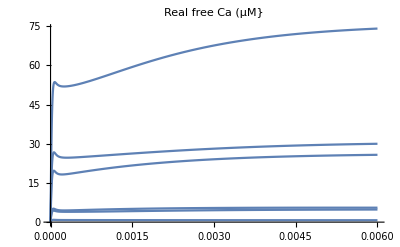

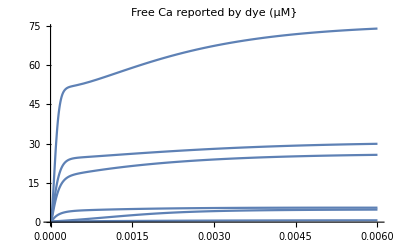

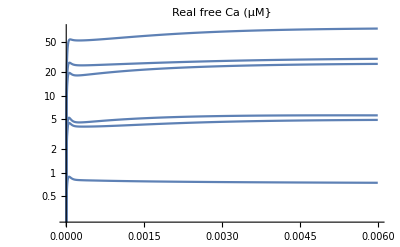

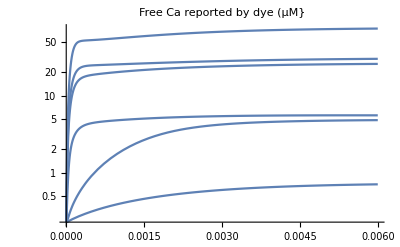

{7.03073×10^-7,4.79194×10^-6,5.53376×10^-6,0.0000257412,0.0000299583,0.0000740312}

```mathematica
Plot[10^6*CaListReal,{tt,0,TimeWindow},PlotLabel->"Real free Ca (µM}"]
Plot[10^6*CaListDye,{tt,0,TimeWindow},PlotLabel->"Free Ca reported by dye (µM}"]
LogPlot[10^6*CaListReal,{tt,0,TimeWindow},PlotLabel->"Real free Ca (µM}"]
LogPlot[10^6*CaListDye,{tt,0,TimeWindow},PlotLabel->"Free Ca reported by dye (µM}"]
CaListDyePeak=Table[NMaximize[{CaListDye[[nn]][[1]][[1]],0≤tt≤TimeWindow},tt][[1]],{nn,Length[CaListDye]}](*"[[1]][[1]]" is neede to get rid of these brackets {{}}*)
```

```mathematica
runs=Length[CaListDyePeak];
```

# Release scheme and start values

## Define release scheme

```mathematica
nStates=7;
mat=Table[0,{nStates},{nStates}];
```

### forward rates

```mathematica
from=1;(*0 ca bound*)
kk=5kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=2;
kk=4 kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=3;
kk=3 kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=4;
kk=2 kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=5;(*4 ca bound*)
kk=kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=6;(*5 ca bound*)
kk=gamma;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;
```

### backwards rates

```mathematica
from=2;(*1 ca bound*)
kk=koff b^0;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;

from=3;
kk=2 koff b^1;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;

from=4;
kk=3 koff b^2;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;

from=5;
kk=4 koff b^3;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;

from=6;(*5 ca bound*)
kk=5 koff b^4;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;
```

### outflux from matrix

```mathematica
mat[[1,1]]+=-kunfill;(* is multiplied by ss1[t] *)
```

### influx in matrix

```mathematica
mat[[1,1]]+=(1/ss1[t])kfill  fillStateSS[t];(* (1/ss1[t]) is needed to merge the fillState Diff Eq. in the matrix format. Note ss1[t] is never 0 *)
```

### Matrix

```mathematica
mat//TableForm
```

-5 kon-kunfill+(kfill fillStateSS[t])/ss1[t] | koff | 0 | 0 | 0 | 0 | 0
5 kon | -koff-4 kon | 2 b koff | 0 | 0 | 0 | 0
0 | 4 kon | -2 b koff-3 kon | 3 b^2 koff | 0 | 0 | 0
0 | 0 | 3 kon | -3 b^2 koff-2 kon | 4 b^3 koff | 0 | 0
0 | 0 | 0 | 2 kon | -4 b^3 koff-kon | 5 b^4 koff | 0
0 | 0 | 0 | 0 | kon | -gamma-5 b^4 koff | 0
0 | 0 | 0 | 0 | 0 | gamma | 0

## Startvalues

```mathematica
linInterpol[x_,a_,b_]:=a+x*(b-a);
```

```mathematica
q10=2.3;
tempFact=q10^((37-24)/10);
```

```mathematica
Clear[caFunc,kprimScheme];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)

caRest=CaRest;(*227nM see above*)

affinityFactor=3.0;
konScheme=linInterpol[sitePlugging[t],
caFunc[t] Sqrt[affinityFactor] tempFact 1.*^8,
0.1 caFunc[t] Sqrt[affinityFactor] tempFact 1.*^8
];(*M^-1 s^-1*)

koffScheme=linInterpol[sitePlugging[t],
(1/Sqrt[affinityFactor])tempFact 15000,
0.4 (1/Sqrt[affinityFactor])tempFact 15000
];(*s^-1*)
gammaScheme=tempFact 6000;(*s^-1*)
bScheme=0.25;

KdPrim=2.*^-6;
kprimScheme =2.5+ 60.(caFunc[t]/(KdPrim+caFunc[t]));
kunprimScheme=2.5+60.(caRest/(KdPrim+caRest));

KdFill=2.*^-6;
kfillScheme=  100+800.(caFunc[t]/(KdFill+caFunc[t]));
kunfillScheme=100+800.(caRest/(KdFill+caRest));


repl={
kon -> konScheme,
koff -> koffScheme ,
gamma -> gammaScheme ,
 b-> bScheme,

kprim-> kprimScheme ,
kunprim-> kunprimScheme ,

kfill-> kfillScheme ,
kunfill-> kunfillScheme 

(*
kbasal-> kbasalScheme ,
kunfill-> kunfillScheme 
*)
};
```

```mathematica
tauOfDecayOfUncagedCa=0.4;
```

```mathematica
siteClearanceTau=0.04;
```

## Initial occupancy

0.791348

0.302831

0.242117

3.26845

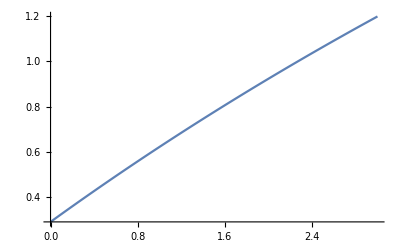

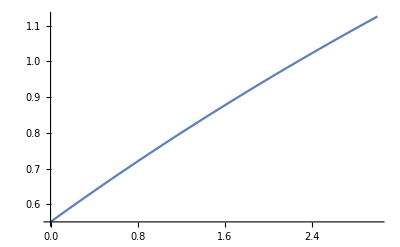

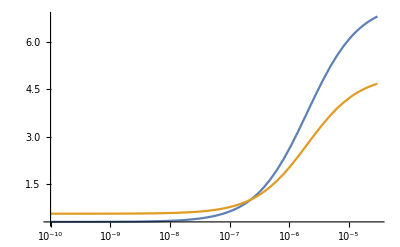

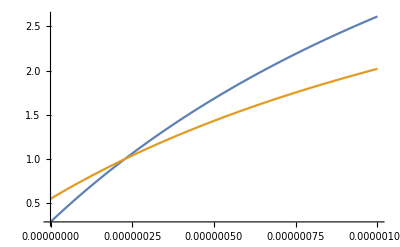

```mathematica
(*test initial equilibrium occupancy*)
caFunc[t_]:=caTmp;
fillStateSSInitial=kprimScheme/kunprimScheme;
ss0Initial=fillStateSSInitial*kfillScheme/kunfillScheme;
(ss0Initial/.caTmp->180*^-9)
(ss0Initial/.caTmp->50*^-9)
(ss0Initial/.caTmp->30*^-9)
(ss0Initial/.caTmp->180*^-9)/(ss0Initial/.caTmp->30*^-9)
(*test initial *)
Plot[kprimScheme/kunprimScheme,{caTmp,0,300*^-9}]
Plot[kfillScheme/kunfillScheme,{caTmp,0,300*^-9}]
LogLinearPlot[{kprimScheme/kunprimScheme,kfillScheme/kunfillScheme},{caTmp,.1*^-9,30*^-6},PlotRange->All]
Plot[{kprimScheme/kunprimScheme,kfillScheme/kunfillScheme},{caTmp,.1*^-9,1*^-6},PlotRange->All]
```

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRest;
kprimScheme
kunprimScheme
fillStateSSInitial=kprimScheme/kunprimScheme
kfillScheme
kunfillScheme
ss0Initial=fillStateSSInitial*kfillScheme/kunfillScheme
```

8.61585

8.61585

1.

181.545

181.545

1.

```mathematica
caRest
```

2.27×10^-7

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
ss[t_]={ss1[t],ss2[t],ss3[t],ss4[t],ss5[t],ss6[t],ss7[t]};
eq={ss'[t]==(mat/.repl).ss[t],
ss[0]=={ss0Initial,0.,0.,0.,0.,0.,0.},
(fillStateSS'[t]==kprim -kunprim  fillStateSS[t]-kfill fillStateSS[t]+kunfill  ss1[t])/.repl,
fillStateSS[0]==fillStateSSInitial,
sitePlugging'[t]==(1-sitePlugging[t])ss7'[t]-siteClearanceTau sitePlugging[t],
sitePlugging[0]==0
};
```

## Print diff eq.

```mathematica
mat
```

{{-5 kon-kunfill+(kfill fillStateSS[t])/ss1[t],koff,0,0,0,0,0},{5 kon,-koff-4 kon,2 b koff,0,0,0,0},{0,4 kon,-2 b koff-3 kon,3 b^2 koff,0,0,0},{0,0,3 kon,-3 b^2 koff-2 kon,4 b^3 koff,0,0},{0,0,0,2 kon,-4 b^3 koff-kon,5 b^4 koff,0},{0,0,0,0,kon,-gamma-5 b^4 koff,0},{0,0,0,0,0,gamma,0}}

```mathematica
repl
```

{kon→5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t],koff→25572.7-15343.6 sitePlugging[t],gamma→17717.3,b→0.25,kprim→2.5+(60. caFunc[t])/(2.×10^-6+caFunc[t]),kunprim→8.61585,kfill→100+(800. caFunc[t])/(2.×10^-6+caFunc[t]),kunfill→181.545}

```mathematica
mat/.repl
```

{{-181.545-5 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t])+((100+(800. caFunc[t])/(2.×10^-6+caFunc[t])) fillStateSS[t])/ss1[t],25572.7-15343.6 sitePlugging[t],0,0,0,0,0},{5 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),-25572.7+15343.6 sitePlugging[t]-4 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),0.5 (25572.7-15343.6 sitePlugging[t]),0,0,0,0},{0,4 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),-0.5 (25572.7-15343.6 sitePlugging[t])-3 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),0.1875 (25572.7-15343.6 sitePlugging[t]),0,0,0},{0,0,3 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),-0.1875 (25572.7-15343.6 sitePlugging[t])-2 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),0.0625 (25572.7-15343.6 sitePlugging[t]),0,0},{0,0,0,2 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]),-5.11454×10^8 caFunc[t]-0.0625 (25572.7-15343.6 sitePlugging[t])+4.60309×10^8 caFunc[t] sitePlugging[t],0.0195313 (25572.7-15343.6 sitePlugging[t]),0},{0,0,0,0,5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t],-17717.3-0.0195313 (25572.7-15343.6 sitePlugging[t]),0},{0,0,0,0,0,17717.3,0}}

```mathematica
eq
```

{{ss1'[t],ss2'[t],ss3'[t],ss4'[t],ss5'[t],ss6'[t],ss7'[t]}=={(-181.545-5 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t])+((100+(800. caFunc[t])/(2.×10^-6+caFunc[t])) fillStateSS[t])/ss1[t]) ss1[t]+(25572.7-15343.6 sitePlugging[t]) ss2[t],5 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]) ss1[t]+(-25572.7+15343.6 sitePlugging[t]-4 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t])) ss2[t]+0.5 (25572.7-15343.6 sitePlugging[t]) ss3[t],4 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]) ss2[t]+(-0.5 (25572.7-15343.6 sitePlugging[t])-3 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t])) ss3[t]+0.1875 (25572.7-15343.6 sitePlugging[t]) ss4[t],3 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]) ss3[t]+(-0.1875 (25572.7-15343.6 sitePlugging[t])-2 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t])) ss4[t]+0.0625 (25572.7-15343.6 sitePlugging[t]) ss5[t],2 (5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]) ss4[t]+(-5.11454×10^8 caFunc[t]-0.0625 (25572.7-15343.6 sitePlugging[t])+4.60309×10^8 caFunc[t] sitePlugging[t]) ss5[t]+0.0195313 (25572.7-15343.6 sitePlugging[t]) ss6[t],(5.11454×10^8 caFunc[t]-4.60309×10^8 caFunc[t] sitePlugging[t]) ss5[t]+(-17717.3-0.0195313 (25572.7-15343.6 sitePlugging[t])) ss6[t],17717.3 ss6[t]},{ss1[0],ss2[0],ss3[0],ss4[0],ss5[0],ss6[0],ss7[0]}=={1.,0.,0.,0.,0.,0.,0.},fillStateSS'[t]==2.5+(60. caFunc[t])/(2.×10^-6+caFunc[t])-8.61585 fillStateSS[t]-(100+(800. caFunc[t])/(2.×10^-6+caFunc[t])) fillStateSS[t]+181.545 ss1[t],fillStateSS[0]==1.,sitePlugging'[t]==-0.04 sitePlugging[t]+(1-sitePlugging[t]) ss7'[t],sitePlugging[0]==0}

## Solve all states

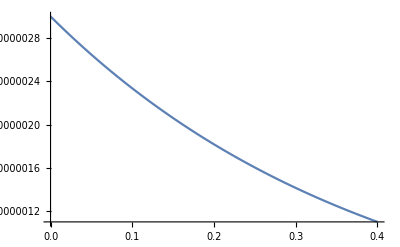

```mathematica
caFunc[t_]:=3*^-6*Exp[-t/tauOfDecayOfUncagedCa];;
Plot[caFunc[t],{t,0,0.4},PlotRange->All]
```

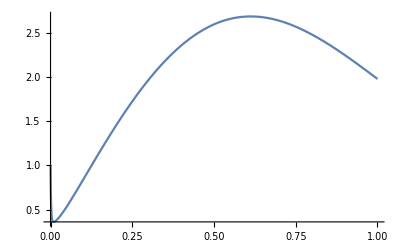

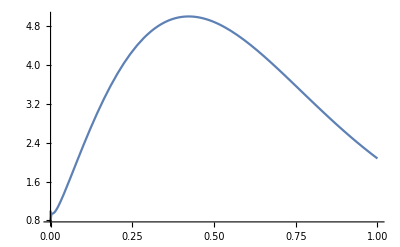

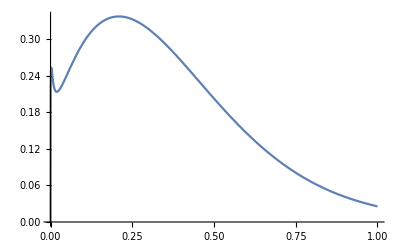

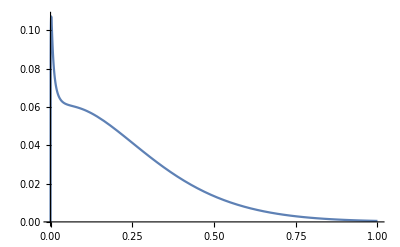

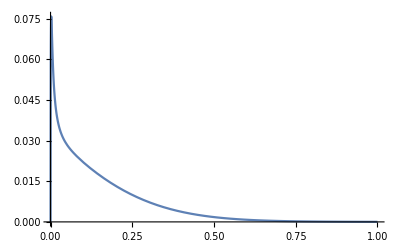

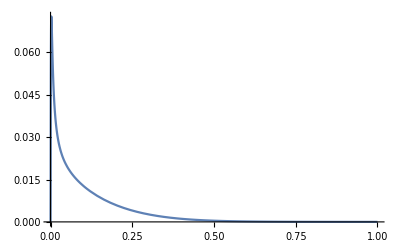

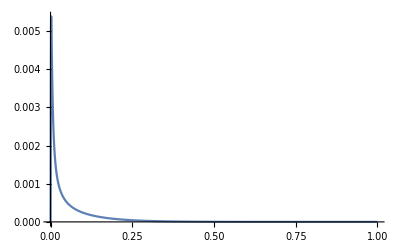

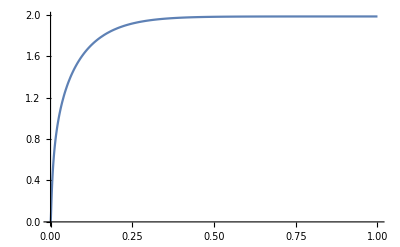

```mathematica
merkSS=NDSolve[eq,{fillStateSS,ss1,ss2,ss3,ss4,ss5,ss6,ss7,sitePlugging},{t,0,10.}];
tEndForPlot=1.;
Plot[(fillStateSS[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss1[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss2[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss3[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss4[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss5[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss6[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss7[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
Plot[(sitePlugging[t]/.merkSS),{t,0,tEndForPlot},PlotRange->All]
```

# Loop

## make lists for later

```mathematica
simCaList=Table[0,{runs}];
simParamNv=Table[0,{7},{runs}];
```

### C5

```mathematica
baselineC5=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataC5}];
(*Lists for saving data within loop*)
imParamNoiseC5=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianC5=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1C5=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2C5=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### C10

```mathematica
baselineC10=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataC10}];
(*Lists for saving data within loop*)
simParamNoiseC10=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianC10=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1C10=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2C10=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### D

```mathematica
baselineD=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataD}];
(*Lists for saving data within loop*)
simParamNoiseD=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianD=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1D=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2D=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### Long

```mathematica
baselineLong=Table[{ttt,0},{ttt,-0.05,-1*^-6,dtOfDataLong}];
```

## Loop

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 0.703073 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

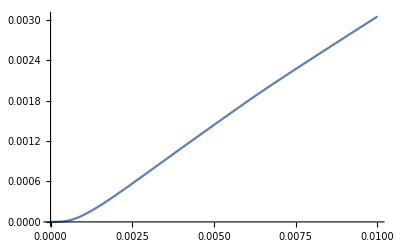

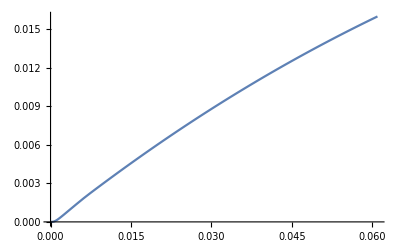

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

-------------------------------------------------------------------------- C5

-------------------------------------------------------------------------- C10

-------------------------------------------------------------------------- D

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 4.79194 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

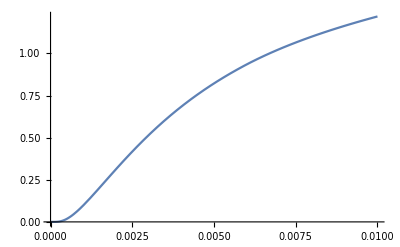

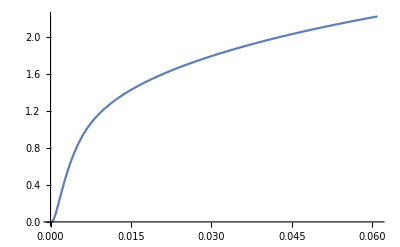

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-------------------------------------------------------------------------- C5

Set::noval: Symbol simParamNoiseC5 in part assignment does not have an immediate value.

General::stop: Further output of Set::noval will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Part::partd: Part specification simParamNoiseC5⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification simParamNoiseC5⟦6,1⟧ is longer than depth of object.

Part::partd: Part specification simParamNoiseC5⟦11,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

take mono

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

take mono

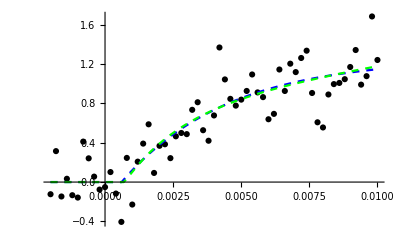

Mono: chi2 = simParamNoiseC5⟦2,3⟧     d = simParamNoiseC5⟦2,3⟧     a = simParamNoiseC5⟦4,3⟧     t = 1/simParamNoiseC5⟦5,3⟧

Bi: ratio chi2Mono/chi2Bi = simParamNoiseC5⟦6,3⟧     d = simParamNoiseC5⟦7,3⟧     a = simParamNoiseC5⟦8,3⟧     a1 = simParamNoiseC5⟦9,3⟧     t1 =1/simParamNoiseC5⟦10,3⟧     t2 = 1/simParamNoiseC5⟦11,3⟧

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

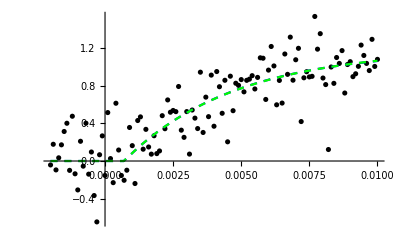

Mono: chi2 = 7.08688     d = 7.08688     a = 1.17872     t = 0.00403296

Bi: ratio chi2Mono/chi2Bi = 0.999794     d = 0.0007     a = 1.44509     a1 = 1.12956     t1 =0.00391193     t2 = 0.070724

Quantile::empt: Argument {} should be a non-empty list.

General::stop: Further output of Quantile::empt will be suppressed during this calculation.

-------------------------------------------------------------------------- D

take mono

take mono

take mono

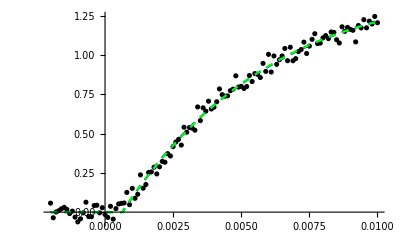

Mono: chi2 = 0.158654     d = 0.158654     a = 1.49144     t = 0.00550646

Bi: ratio chi2Mono/chi2Bi = 1.01159     d = 0.000623127     a = 0.86273     a1 = 2.87366     t1 =0.00768285     t2 = 0.0181125

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 5.53376 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

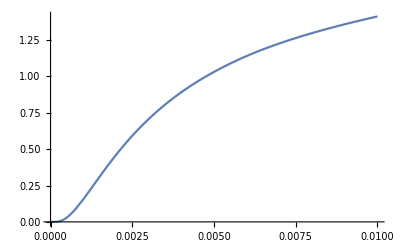

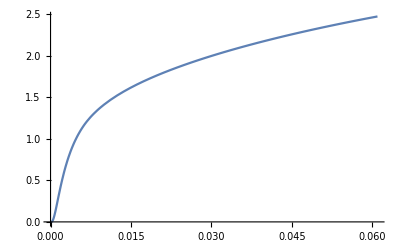

-------------------------------------------------------------------------- C5

take mono

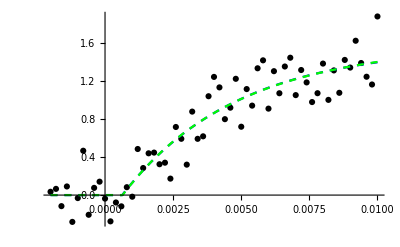

Mono: chi2 = simParamNoiseC5⟦2,3⟧     d = simParamNoiseC5⟦2,3⟧     a = simParamNoiseC5⟦4,3⟧     t = 1/simParamNoiseC5⟦5,3⟧

Bi: ratio chi2Mono/chi2Bi = simParamNoiseC5⟦6,3⟧     d = simParamNoiseC5⟦7,3⟧     a = simParamNoiseC5⟦8,3⟧     a1 = simParamNoiseC5⟦9,3⟧     t1 =1/simParamNoiseC5⟦10,3⟧     t2 = 1/simParamNoiseC5⟦11,3⟧

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

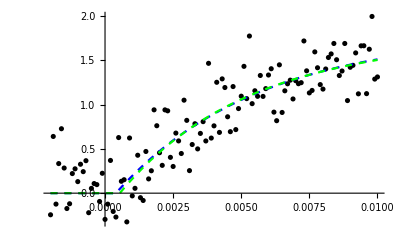

Mono: chi2 = 8.52092     d = 8.52092     a = 1.79507     t = 0.0052043

Bi: ratio chi2Mono/chi2Bi = 0.99677     d = 0.000541875     a = 1.82858     a1 = 1.33796     t1 =0.00416516     t2 = 0.00971541

-------------------------------------------------------------------------- D

take mono

take mono

take mono

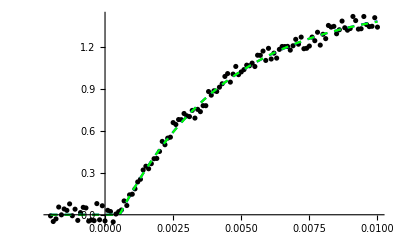

Mono: chi2 = 0.150791     d = 0.150791     a = 1.52878     t = 0.00397755

Bi: ratio chi2Mono/chi2Bi = 1.00064     d = 0.000535539     a = 1.481     a1 = 1.94351     t1 =0.00439514     t2 = 0.00743034

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 25.7412 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

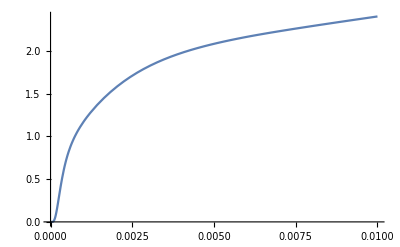

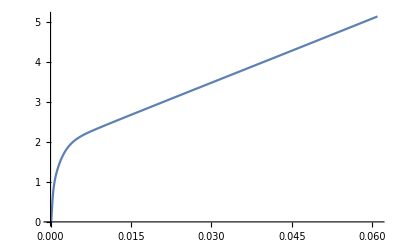

-------------------------------------------------------------------------- C5

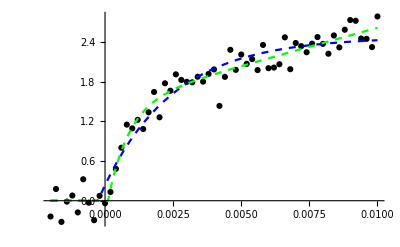

Mono: chi2 = simParamNoiseC5⟦2,3⟧     d = simParamNoiseC5⟦2,3⟧     a = simParamNoiseC5⟦4,3⟧     t = 1/simParamNoiseC5⟦5,3⟧

Bi: ratio chi2Mono/chi2Bi = simParamNoiseC5⟦6,3⟧     d = simParamNoiseC5⟦7,3⟧     a = simParamNoiseC5⟦8,3⟧     a1 = simParamNoiseC5⟦9,3⟧     t1 =1/simParamNoiseC5⟦10,3⟧     t2 = 1/simParamNoiseC5⟦11,3⟧

-------------------------------------------------------------------------- C10

take bi

take bi

take bi

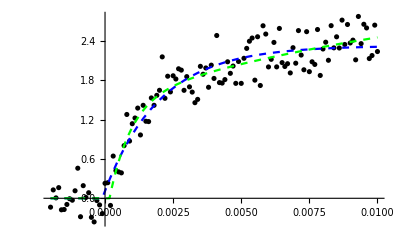

Mono: chi2 = 6.84202     d = 6.84202     a = 2.32614     t = 0.00202853

Bi: ratio chi2Mono/chi2Bi = 1.0904     d = 0.00016458     a = 3.45458     a1 = 1.50402     t1 =0.000799165     t2 = 0.0147441

-------------------------------------------------------------------------- D

take bi

take bi

take bi

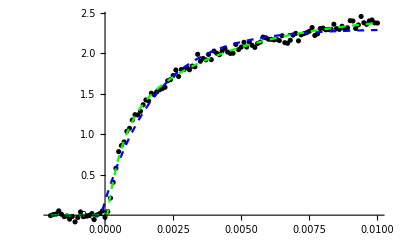

Mono: chi2 = 0.623135     d = 0.623135     a = 2.3009     t = 0.00192783

Bi: ratio chi2Mono/chi2Bi = 3.66281     d = 0.0000793084     a = 2.50245     a1 = 1.10304     t1 =0.000577102     t2 = 0.00413312

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 29.9583 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

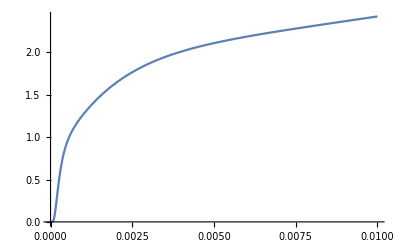

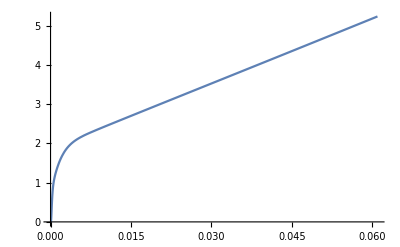

-------------------------------------------------------------------------- C5

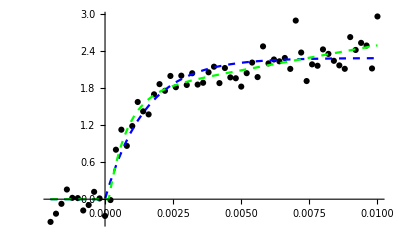

Mono: chi2 = simParamNoiseC5⟦2,3⟧     d = simParamNoiseC5⟦2,3⟧     a = simParamNoiseC5⟦4,3⟧     t = 1/simParamNoiseC5⟦5,3⟧

Bi: ratio chi2Mono/chi2Bi = simParamNoiseC5⟦6,3⟧     d = simParamNoiseC5⟦7,3⟧     a = simParamNoiseC5⟦8,3⟧     a1 = simParamNoiseC5⟦9,3⟧     t1 =1/simParamNoiseC5⟦10,3⟧     t2 = 1/simParamNoiseC5⟦11,3⟧

-------------------------------------------------------------------------- C10

take mono

take bi

take bi

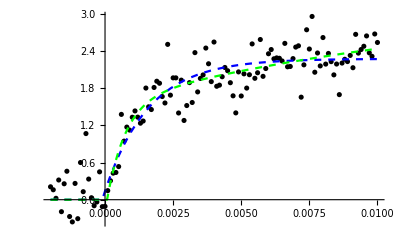

Mono: chi2 = 10.4883     d = 10.4883     a = 2.2743     t = 0.00160435

Bi: ratio chi2Mono/chi2Bi = 1.09923     d = 0.0000747615     a = 3.29227     a1 = 1.57775     t1 =0.000681779     t2 = 0.0142666

-------------------------------------------------------------------------- D

take bi

take bi

take bi

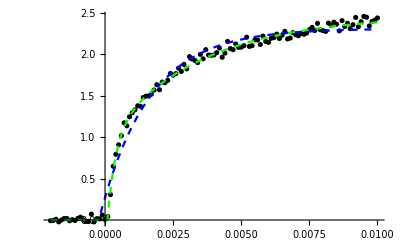

Mono: chi2 = 0.91061     d = 0.91061     a = 2.30711     t = 0.00181864

Bi: ratio chi2Mono/chi2Bi = 4.79737     d = 0.0000900976     a = 2.46542     a1 = 1.0158     t1 =0.000302678     t2 = 0.00344934

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 74.0312 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

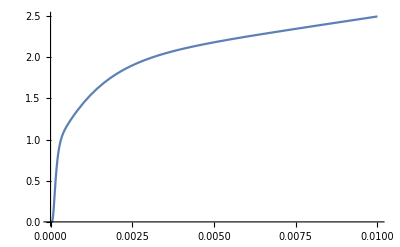

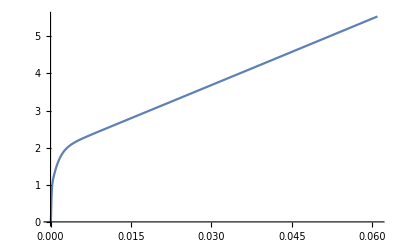

-------------------------------------------------------------------------- C5

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: Exp[-736.49] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-793.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-849.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

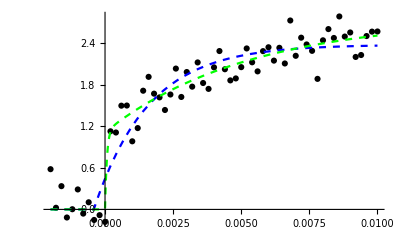

Mono: chi2 = simParamNoiseC5⟦2,3⟧     d = simParamNoiseC5⟦2,3⟧     a = simParamNoiseC5⟦4,3⟧     t = 1/simParamNoiseC5⟦5,3⟧

Bi: ratio chi2Mono/chi2Bi = simParamNoiseC5⟦6,3⟧     d = simParamNoiseC5⟦7,3⟧     a = simParamNoiseC5⟦8,3⟧     a1 = simParamNoiseC5⟦9,3⟧     t1 =1/simParamNoiseC5⟦10,3⟧     t2 = 1/simParamNoiseC5⟦11,3⟧

-------------------------------------------------------------------------- C10

take bi

take mono

take bi

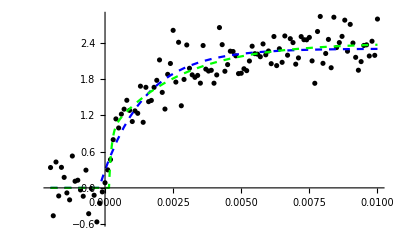

Mono: chi2 = 8.52843     d = 8.52843     a = 2.29944     t = 0.00158323

Bi: ratio chi2Mono/chi2Bi = 1.07682     d = 0.000145139     a = 2.39724     a1 = 0.936027     t1 =0.0000897784     t2 = 0.00259214

-------------------------------------------------------------------------- D

take bi

take bi

take bi

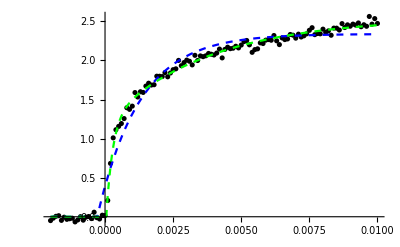

Mono: chi2 = 1.41395     d = 1.41395     a = 2.33924     t = 0.00155065

Bi: ratio chi2Mono/chi2Bi = 5.74032     d = 0.0000457876     a = 2.54393     a1 = 1.22128     t1 =0.000236239     t2 = 0.00374787

```mathematica
For[r=1,r≤runs,r+=1,
myCaNow=CaListDyePeak[[r]];
lastSimulatedCaListReal=CaListReal[[r]][[1]][[1]]/.tt->TimeWindow;(*"[[1]][[1]]" is neede to get rid of these brackets {{}}*)
Print["-------------------------------------------------------------------------------------------------------------"];Print["----------------    Ca = ",1*^6 myCaNow," uM         --------------------------------------------------------"];Print["-------------------------------------------------------------------------------------------------------------"];
simCaList[[r]]=myCaNow;
caFunc[ttt_]:=If[ttt<TimeWindow,
CaListReal[[r]][[1]][[1]]/.tt->ttt,(*tt because this is the symbol used in "Calculate Ca transients"*)
lastSimulatedCaListReal*Exp[-ttt/tauOfDecayOfUncagedCa]
];
(* solve Diff Eq.: *)
merkSS=NDSolve[eq,ss7,{t,0,cursorEndLong}]; 
(* plot results: *)
fused[t_]:=ss7[t];
Plot[(fused[t]/.merkSS),{t,0,cursorEnd},PlotRange->All]//Print;
Plot[(fused[t]/.merkSS),{t,0,cursorEndLong},PlotRange->All]//Print;
If[exportYes==1,
toExport=Table[{t,(fused[t]/.merkSS)[[1]]},{t,0.,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" withoutNoise.txt",toExport,"Table"];
];
(* sample data and add baseline: --------*)
tmpCumRelC5=Table[{ttt,(fused[ttt]/.merkSS)[[1]]},{ttt,0.,cursorEnd,dtOfDataC5}];
tmpToFitC5=Catenate[{baselineC5,tmpCumRelC5}];
tmpCumRelC10=Table[{ttt,(fused[ttt]/.merkSS)[[1]]},{ttt,0.,cursorEnd,dtOfDataC10}];
tmpToFitC10=Catenate[{baselineC10,tmpCumRelC10}];
tmpCumRelD=Table[{ttt,(fused[ttt]/.merkSS)[[1]]},{ttt,0.,cursorEnd,dtOfDataD}];
tmpToFitD=Catenate[{baselineD,tmpCumRelD}];
tmpCumRelLong=Table[{ttt,(fused[ttt]/.merkSS)[[1]]},{ttt,0.,cursorEndLong,dtOfDataLong}];
tmpToFitLong=Catenate[{baselineLong,tmpCumRelLong}];

(*---------    get amplitude without noise and without fitting -----------------*)
For[NvCount=1,NvCount≤7,NvCount+=1,
simParamNv[[NvCount,r]]=(fused[timeOfNv[[NvCount]]]/.merkSS)[[1]];(* the [[1]] is somehow needed to get rid of a list structure probably related to the interpolate function*)
];

(*--------------   Startvalues for fit the same for all C5 C10 and D -------------*)
caAdjustedTau1Guess=tau1Guess/((myCaNow/10.*^-6)^4);
caAdjustedTau1Guess=tau1Guess/((myCaNow/10.*^-6)^1);
caAdjustedTau2Guess=10 caAdjustedTau1Guess;
caAdjustedDelayGuess=delayGuess/((myCaNow/10.*^-6)^1);

(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    C5     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- C5"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioC5 myNoiseC5,(*add noise several times and do the fitting and than average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitC5[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseC5]]&/@tmpToFitC5[[All,2]]}];
(*fit mono-exp*)
merk=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=merk[{"BestFitParameters"}];
simParamNoiseC5[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseC5[[2,noiseN]]=merk["ANOVATableSumsOfSquares"][[2]];
(*Print[merk["ANOVATableSumsOfSquares"]];*)
simParamNoiseC5[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseC5[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseC5[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
merk=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=merk[{"BestFitParameters"}];
simParamNoiseC5[[6,noiseN]]=simParamNoiseC5[[2,noiseN]]/merk["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC5[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseC5[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseC5[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseC5[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseC5[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should imporve(=decrease) by >10%*)
(simParamNoiseC5[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC5[[11,noiseN]]/simParamNoiseC5[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[7,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[8,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=simParamNoiseC5[[9,noiseN]];(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[10,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=simParamNoiseC5[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[3,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[4,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[5,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC5[[2,noiseN]],"     d = ",simParamNoiseC5[[2,noiseN]],"     a = ",simParamNoiseC5[[4,noiseN]],"     t = ",1/simParamNoiseC5[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC5[[6,noiseN]],"     d = ",simParamNoiseC5[[7,noiseN]],"     a = ",simParamNoiseC5[[8,noiseN]],"     a1 = ",simParamNoiseC5[[9,noiseN]],"     t1 =",1/simParamNoiseC5[[10,noiseN]],"     t2 = ",1/simParamNoiseC5[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]=Median[simParamNoiseC5[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianC5[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
merk=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=merk[{"BestFitParameters"}];
simParamNoiseC5[[2,noiseN]]=merk["ANOVATableSumsOfSquares"][[2]];
(*Print[merk["ANOVATableSumsOfSquares"]];*)
simParamNoiseC5[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseC5[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseC5[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
merk=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=merk[{"BestFitParameters"}];
simParamNoiseC5[[6,noiseN]]=simParamNoiseC5[[2,noiseN]]/merk["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC5[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseC5[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseC5[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseC5[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseC5[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should imporve(=decrease) by >10%*)
(simParamNoiseC5[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC5[[11,noiseN]]/simParamNoiseC5[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[7,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[8,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=simParamNoiseC5[[9,noiseN]];(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[10,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=simParamNoiseC5[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[3,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[4,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[5,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC5[[2,noiseN]],"     d = ",simParamNoiseC5[[3,noiseN]],"     a = ",simParamNoiseC5[[4,noiseN]],"     t = ",1/simParamNoiseC5[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC5[[6,noiseN]],"     d = ",simParamNoiseC5[[7,noiseN]],"     a = ",simParamNoiseC5[[8,noiseN]],"     a1 = ",simParamNoiseC5[[9,noiseN]],"     t1 =",1/simParamNoiseC5[[10,noiseN]],"     t2 = ",1/simParamNoiseC5[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]=Median[simParamNoiseC5[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]={};
simParamQuantile1C5[[p,r]]={};
simParamQuantile2C5[[p,r]]={};
];
];


(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    C10     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- C10"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioC10 myNoiseC10,(*add noise and do the fitting several times and then average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitC10[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseC10]]&/@tmpToFitC10[[All,2]]}];
(*fit mono-exp*)
merk=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=merk[{"BestFitParameters"}];
simParamNoiseC10[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseC10[[2,noiseN]]=merk["ANOVATableSumsOfSquares"][[2]];
(*Print[merk["ANOVATableSumsOfSquares"]];*)
simParamNoiseC10[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseC10[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseC10[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
merk=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=merk[{"BestFitParameters"}];
simParamNoiseC10[[6,noiseN]]=simParamNoiseC10[[2,noiseN]]/merk["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC10[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseC10[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseC10[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseC10[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseC10[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC10[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC10[[11,noiseN]]/simParamNoiseC10[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[7,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[8,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=simParamNoiseC10[[9,noiseN]];(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[10,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=simParamNoiseC10[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[3,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[4,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[5,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC10[[2,noiseN]],"     d = ",simParamNoiseC10[[2,noiseN]],"     a = ",simParamNoiseC10[[4,noiseN]],"     t = ",1/simParamNoiseC10[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC10[[6,noiseN]],"     d = ",simParamNoiseC10[[7,noiseN]],"     a = ",simParamNoiseC10[[8,noiseN]],"     a1 = ",simParamNoiseC10[[9,noiseN]],"     t1 =",1/simParamNoiseC10[[10,noiseN]],"     t2 = ",1/simParamNoiseC10[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]=Median[simParamNoiseC10[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianC10[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
merk=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=merk[{"BestFitParameters"}];
simParamNoiseC10[[2,noiseN]]=merk["ANOVATableSumsOfSquares"][[2]];
(*Print[merk["ANOVATableSumsOfSquares"]];*)
simParamNoiseC10[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseC10[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseC10[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
merk=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=merk[{"BestFitParameters"}];
simParamNoiseC10[[6,noiseN]]=simParamNoiseC10[[2,noiseN]]/merk["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC10[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseC10[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseC10[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseC10[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseC10[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC10[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC10[[11,noiseN]]/simParamNoiseC10[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[7,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[8,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=simParamNoiseC10[[9,noiseN]];(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[10,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=simParamNoiseC10[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[3,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[4,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[5,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC10[[2,noiseN]],"     d = ",simParamNoiseC10[[3,noiseN]],"     a = ",simParamNoiseC10[[4,noiseN]],"     t = ",1/simParamNoiseC10[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC10[[6,noiseN]],"     d = ",simParamNoiseC10[[7,noiseN]],"     a = ",simParamNoiseC10[[8,noiseN]],"     a1 = ",simParamNoiseC10[[9,noiseN]],"     t1 =",1/simParamNoiseC10[[10,noiseN]],"     t2 = ",1/simParamNoiseC10[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]=Median[simParamNoiseC10[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]={};
simParamQuantile1C10[[p,r]]={};
simParamQuantile2C10[[p,r]]={};
];
];


(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    D     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- D"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioD myNoiseD,(*add noise several times and do the fitting and than average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitD[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseD]]&/@tmpToFitD[[All,2]]}];
(*fit mono-exp*)
merk=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=merk[{"BestFitParameters"}];
simParamNoiseD[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseD[[2,noiseN]]=merk["ANOVATableSumsOfSquares"][[2]];
(*Print[merk["ANOVATableSumsOfSquares"]];*)
simParamNoiseD[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseD[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseD[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
merk=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=merk[{"BestFitParameters"}];
simParamNoiseD[[6,noiseN]]=simParamNoiseD[[2,noiseN]]/merk["ANOVATableSumsOfSquares"][[2]];
simParamNoiseD[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseD[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseD[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseD[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseD[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseD[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseD[[11,noiseN]]/simParamNoiseD[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[7,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[8,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=simParamNoiseD[[9,noiseN]];(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[10,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=simParamNoiseD[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[3,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[4,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[5,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseD[[2,noiseN]],"     d = ",simParamNoiseD[[2,noiseN]],"     a = ",simParamNoiseD[[4,noiseN]],"     t = ",1/simParamNoiseD[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseD[[6,noiseN]],"     d = ",simParamNoiseD[[7,noiseN]],"     a = ",simParamNoiseD[[8,noiseN]],"     a1 = ",simParamNoiseD[[9,noiseN]],"     t1 =",1/simParamNoiseD[[10,noiseN]],"     t2 = ",1/simParamNoiseD[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]=Median[simParamNoiseD[[p,All]]/.NaN->Sequence[]];
simParamQuantile1D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianD[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
merk=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=merk[{"BestFitParameters"}];
simParamNoiseD[[2,noiseN]]=merk["ANOVATableSumsOfSquares"][[2]];
(*Print[merk["ANOVATableSumsOfSquares"]];*)
simParamNoiseD[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseD[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseD[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
merk=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=merk[{"BestFitParameters"}];
simParamNoiseD[[6,noiseN]]=simParamNoiseD[[2,noiseN]]/merk["ANOVATableSumsOfSquares"][[2]];
simParamNoiseD[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseD[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseD[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseD[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseD[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseD[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseD[[11,noiseN]]/simParamNoiseD[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[7,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[8,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=simParamNoiseD[[9,noiseN]];(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[10,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=simParamNoiseD[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[3,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[4,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[5,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseD[[2,noiseN]],"     d = ",simParamNoiseD[[3,noiseN]],"     a = ",simParamNoiseD[[4,noiseN]],"     t = ",1/simParamNoiseD[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseD[[6,noiseN]],"     d = ",simParamNoiseD[[7,noiseN]],"     a = ",simParamNoiseD[[8,noiseN]],"     a1 = ",simParamNoiseD[[9,noiseN]],"     t1 =",1/simParamNoiseD[[10,noiseN]],"     t2 = ",1/simParamNoiseD[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]=Median[simParamNoiseD[[p,All]]/.NaN->Sequence[]];
simParamQuantile1D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]={};
simParamQuantile1D[[p,r]]={};
simParamQuantile2D[[p,r]]={};
];
];
];
```

# Plots

```mathematica
caFact=1*^6;
```

```mathematica
colorA=Green;
colorB=Red;
colorC=Blue;
```

## release rate 1/tau1 (merge of mono 1/tau and bi 1/tau1)

```mathematica
simParam=15;
```

### C5

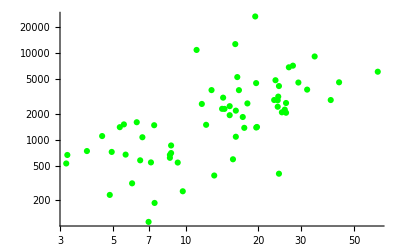

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca, dataT1C5RelRate}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot InvTau1 C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

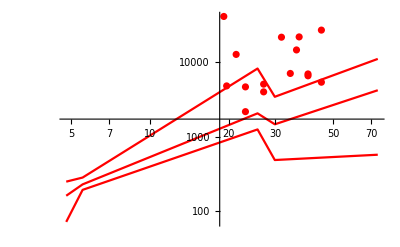

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10RelRate}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot InvTau1 C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

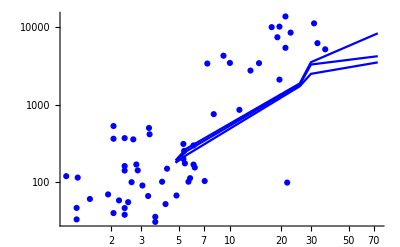

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DRelRate}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 D data.txt",Transpose[{dataT1DCa, dataT1DRelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot InvTau1 D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

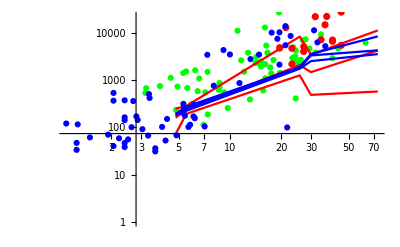

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{0,10}}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->{All,{2,10}}];
```

## delay (mono and bi merged)

```mathematica
simParam=12;
```

```mathematica
Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}]//TableForm
```

0.703073 | 
4.79194 | Median[simParamNoiseC5⟦12,All⟧]
5.53376 | Median[simParamNoiseC5⟦12,All⟧]
25.7412 | Median[simParamNoiseC5⟦12,All⟧]
29.9583 | Median[simParamNoiseC5⟦12,All⟧]
74.0312 | Median[simParamNoiseC5⟦12,All⟧]

### C5

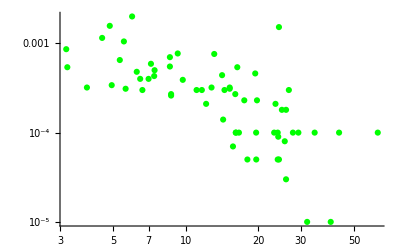

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca, dataT1C5Delay}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot delay C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5Delay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot delay C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

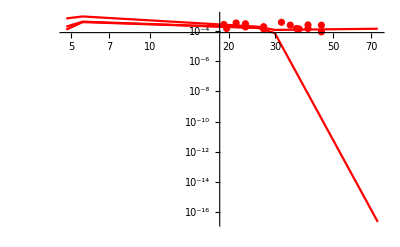

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10Delay}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot delay C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10Delay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot delay C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

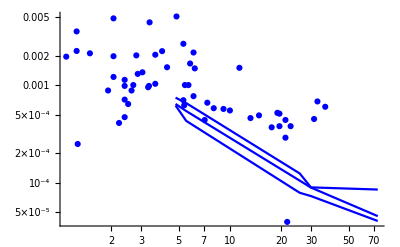

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DDelay}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot delay D data.txt",Transpose[{dataT1DCa, dataT1DDelay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot delay D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

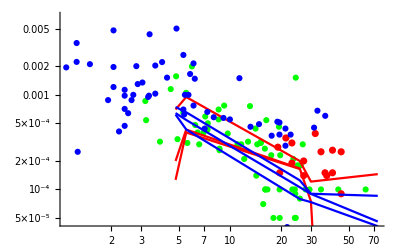

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{-10,-5}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## amp (merge of mono amp and bi amp)

```mathematica
simParam=13;
```

### C5

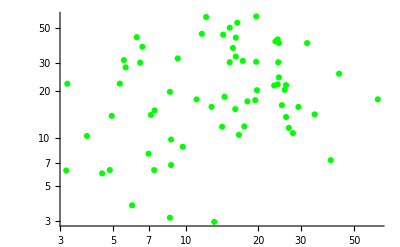

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5Amplitude}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
```

### C10

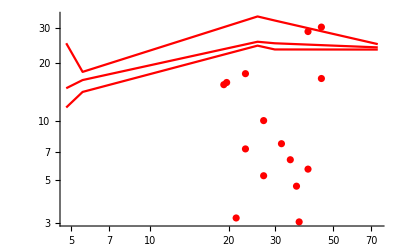

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10Amplitude}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
```

### D

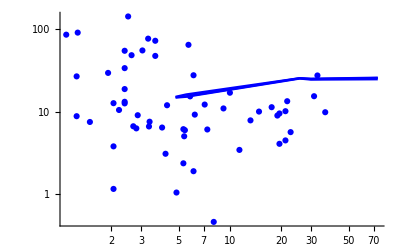

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DAmplitude}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
```

### C5 and C10 and D

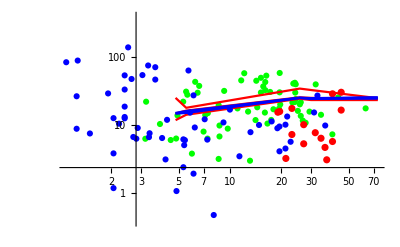

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{-1,6} ]
```

## release rate 1/tau2 of bi fits (if bi is justified)

```mathematica
simParam=16;
```

### C5

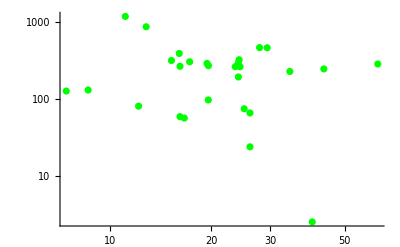

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT2C5Ca, dataT2C5RelRate}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 C5 data.txt",Transpose[{dataT2C5Ca, dataT2C5RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot InvTau2 C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

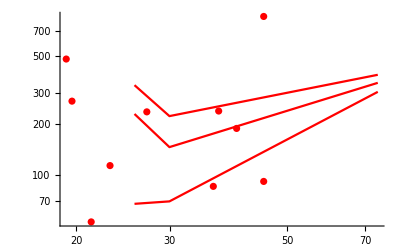

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT2C10Ca, dataT2C10RelRate}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 C10 data.txt",Transpose[{dataT2C10Ca, dataT2C10RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot InvTau2 C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

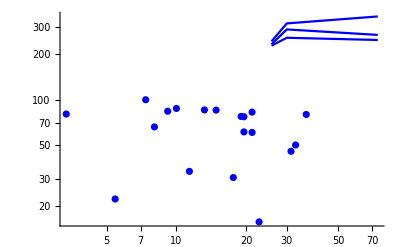

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT2DCa, dataT2DRelRate}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 D data.txt",Transpose[{dataT2DCa, dataT2DRelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot InvTau2 D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

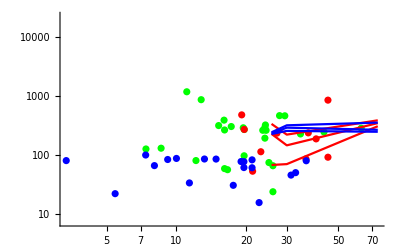

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{2,10}}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## amp1 of bi fits (if bi is justified)

```mathematica
simParam=14;
```

### C5

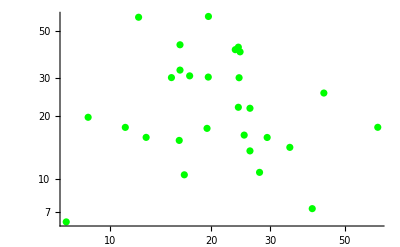

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT2C5Ca, dataT2C5Amplitude1}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{ colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
```

### C10

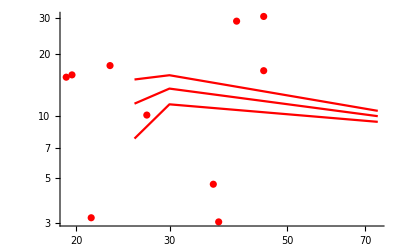

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT2C10Ca, dataT2C10Amplitude1}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
```

### D

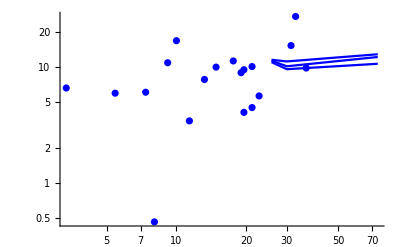

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT2DCa, dataT2DAmplitude1}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianD[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
```

### C5 and C10 and D

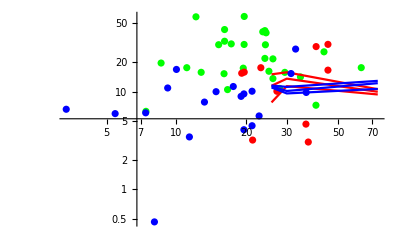

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->All]
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## chi2 mono/bi ratio

```mathematica
simParam=6;
```

### C5

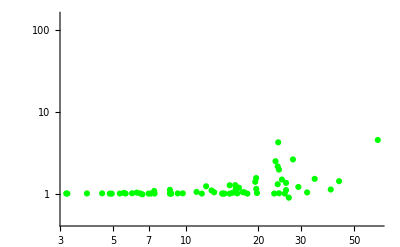

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5ChiRatio}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->{All,{-0.8,5}} ]
If[exportYes==1,
Export["plot chi2Ratio C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5ChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot chi2Ratio C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

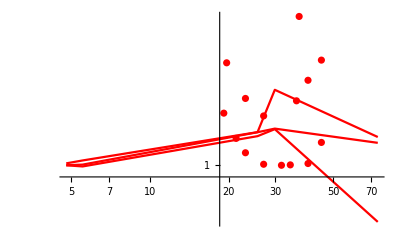

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10ChiRatio}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot chi2Ratio C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10ChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot chi2Ratio C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

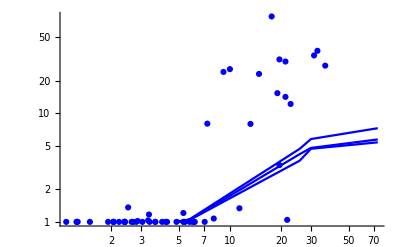

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DChiRatio}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot chi2Ratio D data.txt",Transpose[{dataT1DCa, dataT1DChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot chi2Ratio D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

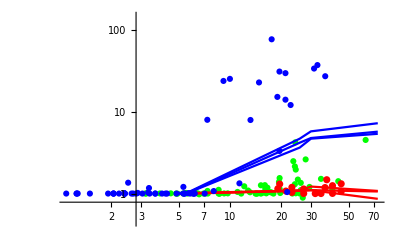

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{-0.8,5}}]
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## Nv

time for Nv (ms) = 0.1

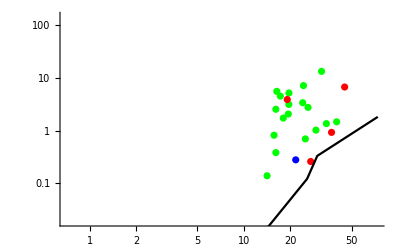

time for Nv (ms) = 0.2

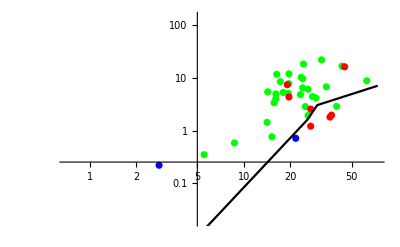

time for Nv (ms) = 1.

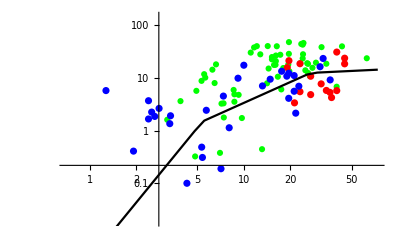

time for Nv (ms) = 5.

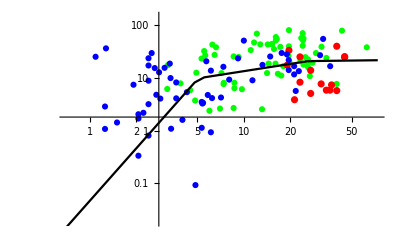

time for Nv (ms) = 10.

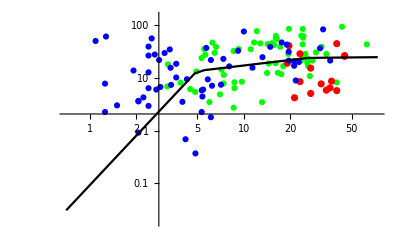

time for Nv (ms) = 100.

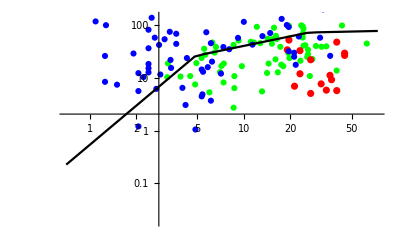

time for Nv (ms) = 400.

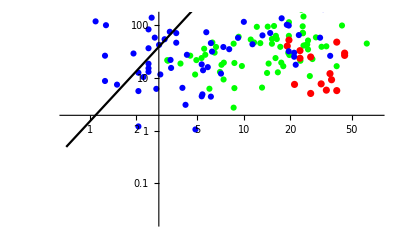

```mathematica
For[NvCount=1,NvCount≤7,NvCount+=1,
Print[" time for Nv (ms) = ",1000*timeOfNv[[NvCount]]];
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5Nv[[NvCount]]}],PlotStyle->{colorA}];gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10Nv[[NvCount]]}],PlotStyle->{colorB}];gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DNv[[NvCount]]}],PlotStyle->{colorC}];gr2=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamNv[[NvCount,All]]}],PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{-4,5}} ]//Print;
];
```

## sustained release 10 to 100 ms

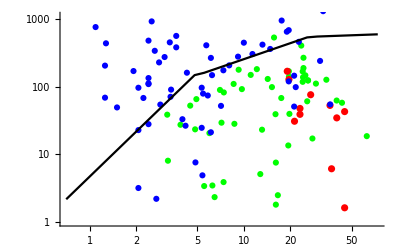

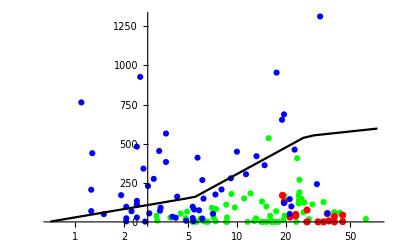

```mathematica
ttt1=Transpose[{dataT1C5Ca,(dataT1C5Nv[[6]]-dataT1C5Nv[[5]])/0.09}];
ttt2=Transpose[{dataT1C10Ca,(dataT1C10Nv[[6]]-dataT1C10Nv[[5]])/0.09}];
ttt3=Transpose[{dataT1DCa,(dataT1DNv[[6]]-dataT1DNv[[5]])/0.09}];
ttt4=Transpose[{caFact simCaList,rrp (simParamNv[[6,All]]-simParamNv[[5,All]])/0.09}];

gr1a=ListLogLogPlot[ttt1,PlotStyle->{colorA}];gr1b=ListLogLogPlot[ttt2,PlotStyle->{colorB}];gr1c=ListLogLogPlot[ttt3,PlotStyle->{colorC}];gr2=ListLogLogPlot[ttt4,PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{0,7}} ]//Print;

gr1a=ListLogLinearPlot[ttt1,PlotStyle->{colorA}];gr1b=ListLogLinearPlot[ttt2,PlotStyle->{colorB}];gr1c=ListLogLinearPlot[ttt3,PlotStyle->{colorC}];gr2=ListLogLinearPlot[ttt4,PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,All} ]//Print;
```

```mathematica
If[exportYes==1,
Export["plot sustained release Cm5 data.txt",ttt1,"Table"];
Export["plot sustained release Cm10 data.txt",ttt2,"Table"];
Export["plot sustained release D data.txt",ttt3,"Table"];
Export["plot sustained release sim.txt",ttt4,"Table"]
];
```

## Nv normalize to the value at 5 ms

```mathematica
timeOfNv
nromPos=5;
1000*timeOfNv[[nromPos]]
```

{0.0001,0.0002,0.001,0.005,0.01,0.1,0.4}

10.

```mathematica
dataT1DNvNorm=Transpose[Transpose[dataT1DNv]/dataT1DNv[[nromPos]]];
dataT1C10NvNorm=Transpose[Transpose[dataT1C10Nv]/dataT1C10Nv[[nromPos]]];
dataT1C5NvNorm=Transpose[Transpose[dataT1C5Nv]/dataT1C5Nv[[nromPos]]];
```

```mathematica
dataT1C5NvNorm//TableForm
```

0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.102935 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.52193×10^-14 | 0.178312 | 0.0755089 | 0.0473226 | 0.0333024 | 0.340245 | 0. | 1.39164×10^-14 | 0.0601626 | 0. | 0. | 7.19133×10^-15 | 0.0241817 | 0.0440838 | 0. | 0.0191435 | 0.114433 | 0. | 0.118442 | 0. | 0.0774881 | 0. | 1.46416×10^-14 | 0.00602208 | 1.02421×10^-14 | 0.0716702 | 0.101175 | 0.115468 | 0. | 0.0110623 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.316273 | 0. | 0. | 0. | 0.0701729 | 0. | 0. | 0. | 0. | 0.0170058 | 0. | 0. | 0. | 0. | 0.12336 | 0.202992 | 0.351351 | 0.188089 | 0.237307 | 0.136209 | 0.564724 | 0. | 0.207552 | 0.139305 | 0. | 0.113553 | 0.11357 | 0.0994779 | 0.0862469 | 0.178169 | 0.0795134 | 0.294241 | 0. | 0.262297 | 0. | 0.14845 | 0. | 0.226711 | 0.0642888 | 0.161145 | 0.177142 | 0.213373 | 0.217604 | 0. | 0.115173 | 0.00975232 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.20362 | 0.265687 | 0.42823 | 0.550679 | 0.804146 | 0.862111 | 0.657036 | 0.804743 | 0.466744 | 0.922133 | 0.226521 | 0. | 0.444507 | 0.589449 | 0. | 0.15518 | 0.367819 | 0.618488 | 0.505051 | 0.547477 | 0.513227 | 0.519289 | 0.933247 | 0.917326 | 0.544754 | 0.830177 | 0.69397 | 0.653131 | 0.639806 | 0.984375 | 0.97219 | 0.730494 | 0.559303 | 0.83967 | 0.731871 | 0.503567 | 0.488021 | 0.36372 | 0.423484 | 0.416379 | 0.740654 | 0.999425 | 0.797225 | 0. | 0.539082 | 0.482694 | 0.90113 | 0.423125 | 0.696723 | 0.629088 | 0.729281 | 0.70682 | 0.127201 | 0.636613 | 0.331405 | 0.368274 | 0.077147 | 0.306211 | 0.418689 | 0.181267 | 0. | 0.232772 | 0. | 0.0592293 | 0.134595
0.719618 | 0.914034 | 0.947765 | 0.995367 | 0.999983 | 0.961307 | 0.985586 | 0.999983 | 0.986917 | 1. | 0.86321 | 0.683794 | 0.967426 | 0.977818 | 0.965586 | 0.708108 | 0.973689 | 0.956794 | 0.984176 | 0.965348 | 0.941072 | 0.896487 | 0.98101 | 0.985262 | 0.880129 | 0.936881 | 0.963176 | 0.841825 | 0.974315 | 1. | 0.98456 | 0.911675 | 0.944403 | 0.953872 | 0.942061 | 0.833228 | 0.867192 | 0.902689 | 0.841473 | 0.835146 | 0.901232 | 1. | 0.967706 | 0.743696 | 0.939188 | 0.889259 | 1. | 0.950512 | 0.90223 | 0.924817 | 0.998695 | 0.997838 | 0.731764 | 0.99577 | 0.911563 | 0.977923 | 0.537561 | 0.918451 | 0.972435 | 0.787082 | 0.953907 | 0.895019 | 0.984865 | 0.685304 | 0.707132
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1.97523 | 1.00693 | 1.44309 | 1.00001 | 1. | 1.38099 | 1.17479 | 1. | 1.00013 | 1. | 1.18393 | 1.53164 | 1.30116 | 1.30623 | 1.03968 | 1.64805 | 1.00052 | 1.01005 | 1.00022 | 1.19403 | 1.51767 | 1.2107 | 1.18462 | 1.26526 | 1.03829 | 1.68326 | 1.36675 | 1.39883 | 1.32694 | 1. | 1.27792 | 1.07205 | 1.14733 | 1.01771 | 1.65534 | 1.12419 | 1.46156 | 1.01176 | 1.0551 | 2.13029 | 1.38531 | 1. | 1.47718 | 1.70375 | 1.34613 | 1.21175 | 1. | 1.00256 | 1.57304 | 1.04225 | 1. | 1. | 1.59812 | 1.00002 | 1.00854 | 1.00034 | 2.65238 | 1.00661 | 1.04431 | 1.30233 | 1.76776 | 1.50246 | 1.00007 | 1.38717 | 1.45179
1.98885 | 1.00693 | 1.64647 | 1.00001 | 1. | 1.52805 | 1.34343 | 1. | 1.00013 | 1. | 1.24117 | 1.79443 | 2.30436 | 2.3269 | 1.17069 | 1.71471 | 1.00052 | 1.01005 | 1.00022 | 1.21138 | 1.65758 | 1.21086 | 1.25309 | 2.14948 | 1.03829 | 2.04028 | 1.52489 | 1.39982 | 1.93919 | 1. | 2.20431 | 1.07205 | 1.33654 | 1.01771 | 2.05226 | 1.12419 | 1.46722 | 1.01176 | 1.0551 | 2.29399 | 2.36374 | 1. | 2.21681 | 1.71285 | 1.66014 | 1.21186 | 1. | 1.00256 | 3.12924 | 1.04225 | 1. | 1. | 1.88985 | 1.00002 | 1.00854 | 1.00034 | 2.67307 | 1.00661 | 1.19026 | 1.37488 | 4.32694 | 3.15888 | 1.00007 | 2.14221 | 1.71564

```mathematica
simParamNv//TableForm
simParamNvNorm=Transpose[Transpose[simParamNv]/simParamNv[[nromPos]]];
simParamNvNorm//TableForm
```

1.15831×10^-8 | 0.0000225289 | 0.0000470166 | 0.0120637 | 0.0330104 | 0.182311
4.04537×10^-7 | 0.000699228 | 0.00131308 | 0.158638 | 0.305208 | 0.713778
0.000100151 | 0.0977688 | 0.154622 | 1.16532 | 1.26874 | 1.44248
0.00143825 | 0.822265 | 1.03048 | 2.08205 | 2.11032 | 2.18122
0.00304654 | 1.21973 | 1.41133 | 2.40188 | 2.42511 | 2.49533
0.022516 | 2.55684 | 2.85988 | 7.23487 | 7.40447 | 7.86461
0.0489061 | 21.376 | 21.9125 | 20.38 | 19.6389 | 23.8767

3.80206×10^-6 | 0.0000184704 | 0.0000333137 | 0.0050226 | 0.0136119 | 0.073061
0.000132786 | 0.000573263 | 0.000930384 | 0.0660475 | 0.125853 | 0.286046
0.0328736 | 0.0801559 | 0.109558 | 0.48517 | 0.523167 | 0.578071
0.472094 | 0.674135 | 0.730146 | 0.866841 | 0.870194 | 0.87412
1. | 1. | 1. | 1. | 1. | 1.
7.39066 | 2.09623 | 2.02637 | 3.01217 | 3.05325 | 3.15173
16.053 | 17.5252 | 15.5262 | 8.485 | 8.09814 | 9.56857

time for Nv (ms) = 0.1

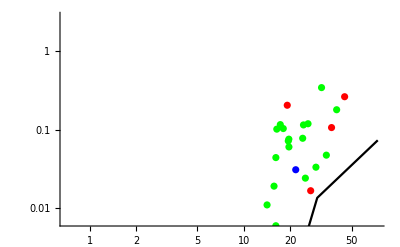

time for Nv (ms) = 0.2

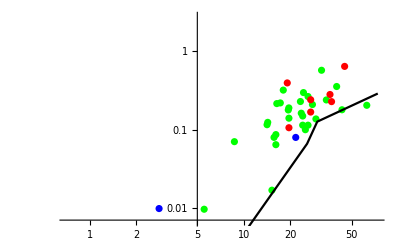

time for Nv (ms) = 1.

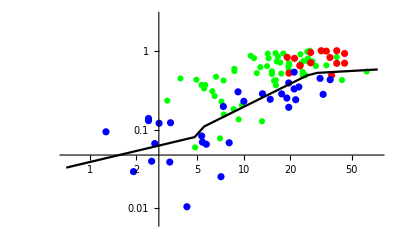

time for Nv (ms) = 5.

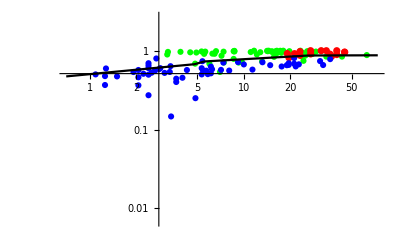

time for Nv (ms) = 10.

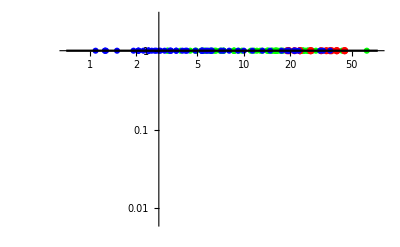

time for Nv (ms) = 100.

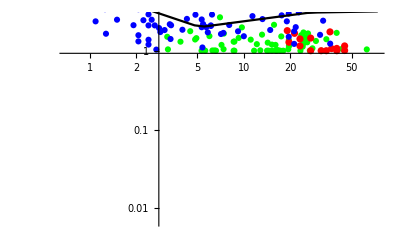

time for Nv (ms) = 400.

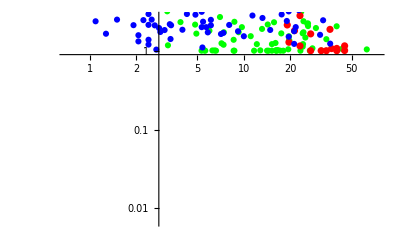

```mathematica
For[NvCount=1,NvCount≤7,NvCount+=1,
Print[" time for Nv (ms) = ",1000*timeOfNv[[NvCount]]];
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5NvNorm[[NvCount]]}],PlotStyle->{colorA}];gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10NvNorm[[NvCount]]}],PlotStyle->{colorB}];gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DNvNorm[[NvCount]]}],PlotStyle->{colorC}];gr2=ListLogLogPlot[Transpose[{caFact simCaList, simParamNvNorm[[NvCount,All]]}],PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{-5,1}} ]//Print;
];
```

## Export Nv

```mathematica
If[exportYes==1,
Export["Nv export Ca,0.0001,0.0002,0.001,0.005,0.01,0.1,0.4.txt",Transpose[Prepend[simParamNv,caFact simCaList]],"Table"];
];
```

## Print some values

### C5

```mathematica
Transpose[simParamMedianC5]//TableForm
Transpose[simParamQuantile1C5]//TableForm
Transpose[simParamQuantile2C5]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Median[simParamNoiseC5⟦1,All⟧] | Median[simParamNoiseC5⟦2,All⟧] | Median[simParamNoiseC5⟦3,All⟧] | Median[simParamNoiseC5⟦4,All⟧] | Median[simParamNoiseC5⟦5,All⟧] | Median[simParamNoiseC5⟦6,All⟧] | Median[simParamNoiseC5⟦7,All⟧] | Median[simParamNoiseC5⟦8,All⟧] | Median[simParamNoiseC5⟦9,All⟧] | Median[simParamNoiseC5⟦10,All⟧] | Median[simParamNoiseC5⟦11,All⟧] | Median[simParamNoiseC5⟦12,All⟧] | Median[simParamNoiseC5⟦13,All⟧] | Median[simParamNoiseC5⟦14,All⟧] | Median[simParamNoiseC5⟦15,All⟧] | Median[simParamNoiseC5⟦16,All⟧]
Median[simParamNoiseC5⟦1,All⟧] | Median[simParamNoiseC5⟦2,All⟧] | Median[simParamNoiseC5⟦3,All⟧] | Median[simParamNoiseC5⟦4,All⟧] | Median[simParamNoiseC5⟦5,All⟧] | Median[simParamNoiseC5⟦6,All⟧] | Median[simParamNoiseC5⟦7,All⟧] | Median[simParamNoiseC5⟦8,All⟧] | Median[simParamNoiseC5⟦9,All⟧] | Median[simParamNoiseC5⟦10,All⟧] | Median[simParamNoiseC5⟦11,All⟧] | Median[simParamNoiseC5⟦12,All⟧] | Median[simParamNoiseC5⟦13,All⟧] | Median[simParamNoiseC5⟦14,All⟧] | Median[simParamNoiseC5⟦15,All⟧] | Median[simParamNoiseC5⟦16,All⟧]
Median[simParamNoiseC5⟦1,All⟧] | Median[simParamNoiseC5⟦2,All⟧] | Median[simParamNoiseC5⟦3,All⟧] | Median[simParamNoiseC5⟦4,All⟧] | Median[simParamNoiseC5⟦5,All⟧] | Median[simParamNoiseC5⟦6,All⟧] | Median[simParamNoiseC5⟦7,All⟧] | Median[simParamNoiseC5⟦8,All⟧] | Median[simParamNoiseC5⟦9,All⟧] | Median[simParamNoiseC5⟦10,All⟧] | Median[simParamNoiseC5⟦11,All⟧] | Median[simParamNoiseC5⟦12,All⟧] | Median[simParamNoiseC5⟦13,All⟧] | Median[simParamNoiseC5⟦14,All⟧] | Median[simParamNoiseC5⟦15,All⟧] | Median[simParamNoiseC5⟦16,All⟧]
Median[simParamNoiseC5⟦1,All⟧] | Median[simParamNoiseC5⟦2,All⟧] | Median[simParamNoiseC5⟦3,All⟧] | Median[simParamNoiseC5⟦4,All⟧] | Median[simParamNoiseC5⟦5,All⟧] | Median[simParamNoiseC5⟦6,All⟧] | Median[simParamNoiseC5⟦7,All⟧] | Median[simParamNoiseC5⟦8,All⟧] | Median[simParamNoiseC5⟦9,All⟧] | Median[simParamNoiseC5⟦10,All⟧] | Median[simParamNoiseC5⟦11,All⟧] | Median[simParamNoiseC5⟦12,All⟧] | Median[simParamNoiseC5⟦13,All⟧] | Median[simParamNoiseC5⟦14,All⟧] | Median[simParamNoiseC5⟦15,All⟧] | Median[simParamNoiseC5⟦16,All⟧]
Median[simParamNoiseC5⟦1,All⟧] | Median[simParamNoiseC5⟦2,All⟧] | Median[simParamNoiseC5⟦3,All⟧] | Median[simParamNoiseC5⟦4,All⟧] | Median[simParamNoiseC5⟦5,All⟧] | Median[simParamNoiseC5⟦6,All⟧] | Median[simParamNoiseC5⟦7,All⟧] | Median[simParamNoiseC5⟦8,All⟧] | Median[simParamNoiseC5⟦9,All⟧] | Median[simParamNoiseC5⟦10,All⟧] | Median[simParamNoiseC5⟦11,All⟧] | Median[simParamNoiseC5⟦12,All⟧] | Median[simParamNoiseC5⟦13,All⟧] | Median[simParamNoiseC5⟦14,All⟧] | Median[simParamNoiseC5⟦15,All⟧] | Median[simParamNoiseC5⟦16,All⟧]

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Quantile[simParamNoiseC5⟦1,All⟧,0.25] | Quantile[simParamNoiseC5⟦2,All⟧,0.25] | Quantile[simParamNoiseC5⟦3,All⟧,0.25] | Quantile[simParamNoiseC5⟦4,All⟧,0.25] | Quantile[simParamNoiseC5⟦5,All⟧,0.25] | Quantile[simParamNoiseC5⟦6,All⟧,0.25] | Quantile[simParamNoiseC5⟦7,All⟧,0.25] | Quantile[simParamNoiseC5⟦8,All⟧,0.25] | Quantile[simParamNoiseC5⟦9,All⟧,0.25] | Quantile[simParamNoiseC5⟦10,All⟧,0.25] | Quantile[simParamNoiseC5⟦11,All⟧,0.25] | Quantile[simParamNoiseC5⟦12,All⟧,0.25] | Quantile[simParamNoiseC5⟦13,All⟧,0.25] | Quantile[simParamNoiseC5⟦14,All⟧,0.25] | Quantile[simParamNoiseC5⟦15,All⟧,0.25] | Quantile[simParamNoiseC5⟦16,All⟧,0.25]
Quantile[simParamNoiseC5⟦1,All⟧,0.25] | Quantile[simParamNoiseC5⟦2,All⟧,0.25] | Quantile[simParamNoiseC5⟦3,All⟧,0.25] | Quantile[simParamNoiseC5⟦4,All⟧,0.25] | Quantile[simParamNoiseC5⟦5,All⟧,0.25] | Quantile[simParamNoiseC5⟦6,All⟧,0.25] | Quantile[simParamNoiseC5⟦7,All⟧,0.25] | Quantile[simParamNoiseC5⟦8,All⟧,0.25] | Quantile[simParamNoiseC5⟦9,All⟧,0.25] | Quantile[simParamNoiseC5⟦10,All⟧,0.25] | Quantile[simParamNoiseC5⟦11,All⟧,0.25] | Quantile[simParamNoiseC5⟦12,All⟧,0.25] | Quantile[simParamNoiseC5⟦13,All⟧,0.25] | Quantile[simParamNoiseC5⟦14,All⟧,0.25] | Quantile[simParamNoiseC5⟦15,All⟧,0.25] | Quantile[simParamNoiseC5⟦16,All⟧,0.25]
Quantile[simParamNoiseC5⟦1,All⟧,0.25] | Quantile[simParamNoiseC5⟦2,All⟧,0.25] | Quantile[simParamNoiseC5⟦3,All⟧,0.25] | Quantile[simParamNoiseC5⟦4,All⟧,0.25] | Quantile[simParamNoiseC5⟦5,All⟧,0.25] | Quantile[simParamNoiseC5⟦6,All⟧,0.25] | Quantile[simParamNoiseC5⟦7,All⟧,0.25] | Quantile[simParamNoiseC5⟦8,All⟧,0.25] | Quantile[simParamNoiseC5⟦9,All⟧,0.25] | Quantile[simParamNoiseC5⟦10,All⟧,0.25] | Quantile[simParamNoiseC5⟦11,All⟧,0.25] | Quantile[simParamNoiseC5⟦12,All⟧,0.25] | Quantile[simParamNoiseC5⟦13,All⟧,0.25] | Quantile[simParamNoiseC5⟦14,All⟧,0.25] | Quantile[simParamNoiseC5⟦15,All⟧,0.25] | Quantile[simParamNoiseC5⟦16,All⟧,0.25]
Quantile[simParamNoiseC5⟦1,All⟧,0.25] | Quantile[simParamNoiseC5⟦2,All⟧,0.25] | Quantile[simParamNoiseC5⟦3,All⟧,0.25] | Quantile[simParamNoiseC5⟦4,All⟧,0.25] | Quantile[simParamNoiseC5⟦5,All⟧,0.25] | Quantile[simParamNoiseC5⟦6,All⟧,0.25] | Quantile[simParamNoiseC5⟦7,All⟧,0.25] | Quantile[simParamNoiseC5⟦8,All⟧,0.25] | Quantile[simParamNoiseC5⟦9,All⟧,0.25] | Quantile[simParamNoiseC5⟦10,All⟧,0.25] | Quantile[simParamNoiseC5⟦11,All⟧,0.25] | Quantile[simParamNoiseC5⟦12,All⟧,0.25] | Quantile[simParamNoiseC5⟦13,All⟧,0.25] | Quantile[simParamNoiseC5⟦14,All⟧,0.25] | Quantile[simParamNoiseC5⟦15,All⟧,0.25] | Quantile[simParamNoiseC5⟦16,All⟧,0.25]
Quantile[simParamNoiseC5⟦1,All⟧,0.25] | Quantile[simParamNoiseC5⟦2,All⟧,0.25] | Quantile[simParamNoiseC5⟦3,All⟧,0.25] | Quantile[simParamNoiseC5⟦4,All⟧,0.25] | Quantile[simParamNoiseC5⟦5,All⟧,0.25] | Quantile[simParamNoiseC5⟦6,All⟧,0.25] | Quantile[simParamNoiseC5⟦7,All⟧,0.25] | Quantile[simParamNoiseC5⟦8,All⟧,0.25] | Quantile[simParamNoiseC5⟦9,All⟧,0.25] | Quantile[simParamNoiseC5⟦10,All⟧,0.25] | Quantile[simParamNoiseC5⟦11,All⟧,0.25] | Quantile[simParamNoiseC5⟦12,All⟧,0.25] | Quantile[simParamNoiseC5⟦13,All⟧,0.25] | Quantile[simParamNoiseC5⟦14,All⟧,0.25] | Quantile[simParamNoiseC5⟦15,All⟧,0.25] | Quantile[simParamNoiseC5⟦16,All⟧,0.25]

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Quantile[simParamNoiseC5⟦1,All⟧,0.75] | Quantile[simParamNoiseC5⟦2,All⟧,0.75] | Quantile[simParamNoiseC5⟦3,All⟧,0.75] | Quantile[simParamNoiseC5⟦4,All⟧,0.75] | Quantile[simParamNoiseC5⟦5,All⟧,0.75] | Quantile[simParamNoiseC5⟦6,All⟧,0.75] | Quantile[simParamNoiseC5⟦7,All⟧,0.75] | Quantile[simParamNoiseC5⟦8,All⟧,0.75] | Quantile[simParamNoiseC5⟦9,All⟧,0.75] | Quantile[simParamNoiseC5⟦10,All⟧,0.75] | Quantile[simParamNoiseC5⟦11,All⟧,0.75] | Quantile[simParamNoiseC5⟦12,All⟧,0.75] | Quantile[simParamNoiseC5⟦13,All⟧,0.75] | Quantile[simParamNoiseC5⟦14,All⟧,0.75] | Quantile[simParamNoiseC5⟦15,All⟧,0.75] | Quantile[simParamNoiseC5⟦16,All⟧,0.75]
Quantile[simParamNoiseC5⟦1,All⟧,0.75] | Quantile[simParamNoiseC5⟦2,All⟧,0.75] | Quantile[simParamNoiseC5⟦3,All⟧,0.75] | Quantile[simParamNoiseC5⟦4,All⟧,0.75] | Quantile[simParamNoiseC5⟦5,All⟧,0.75] | Quantile[simParamNoiseC5⟦6,All⟧,0.75] | Quantile[simParamNoiseC5⟦7,All⟧,0.75] | Quantile[simParamNoiseC5⟦8,All⟧,0.75] | Quantile[simParamNoiseC5⟦9,All⟧,0.75] | Quantile[simParamNoiseC5⟦10,All⟧,0.75] | Quantile[simParamNoiseC5⟦11,All⟧,0.75] | Quantile[simParamNoiseC5⟦12,All⟧,0.75] | Quantile[simParamNoiseC5⟦13,All⟧,0.75] | Quantile[simParamNoiseC5⟦14,All⟧,0.75] | Quantile[simParamNoiseC5⟦15,All⟧,0.75] | Quantile[simParamNoiseC5⟦16,All⟧,0.75]
Quantile[simParamNoiseC5⟦1,All⟧,0.75] | Quantile[simParamNoiseC5⟦2,All⟧,0.75] | Quantile[simParamNoiseC5⟦3,All⟧,0.75] | Quantile[simParamNoiseC5⟦4,All⟧,0.75] | Quantile[simParamNoiseC5⟦5,All⟧,0.75] | Quantile[simParamNoiseC5⟦6,All⟧,0.75] | Quantile[simParamNoiseC5⟦7,All⟧,0.75] | Quantile[simParamNoiseC5⟦8,All⟧,0.75] | Quantile[simParamNoiseC5⟦9,All⟧,0.75] | Quantile[simParamNoiseC5⟦10,All⟧,0.75] | Quantile[simParamNoiseC5⟦11,All⟧,0.75] | Quantile[simParamNoiseC5⟦12,All⟧,0.75] | Quantile[simParamNoiseC5⟦13,All⟧,0.75] | Quantile[simParamNoiseC5⟦14,All⟧,0.75] | Quantile[simParamNoiseC5⟦15,All⟧,0.75] | Quantile[simParamNoiseC5⟦16,All⟧,0.75]
Quantile[simParamNoiseC5⟦1,All⟧,0.75] | Quantile[simParamNoiseC5⟦2,All⟧,0.75] | Quantile[simParamNoiseC5⟦3,All⟧,0.75] | Quantile[simParamNoiseC5⟦4,All⟧,0.75] | Quantile[simParamNoiseC5⟦5,All⟧,0.75] | Quantile[simParamNoiseC5⟦6,All⟧,0.75] | Quantile[simParamNoiseC5⟦7,All⟧,0.75] | Quantile[simParamNoiseC5⟦8,All⟧,0.75] | Quantile[simParamNoiseC5⟦9,All⟧,0.75] | Quantile[simParamNoiseC5⟦10,All⟧,0.75] | Quantile[simParamNoiseC5⟦11,All⟧,0.75] | Quantile[simParamNoiseC5⟦12,All⟧,0.75] | Quantile[simParamNoiseC5⟦13,All⟧,0.75] | Quantile[simParamNoiseC5⟦14,All⟧,0.75] | Quantile[simParamNoiseC5⟦15,All⟧,0.75] | Quantile[simParamNoiseC5⟦16,All⟧,0.75]
Quantile[simParamNoiseC5⟦1,All⟧,0.75] | Quantile[simParamNoiseC5⟦2,All⟧,0.75] | Quantile[simParamNoiseC5⟦3,All⟧,0.75] | Quantile[simParamNoiseC5⟦4,All⟧,0.75] | Quantile[simParamNoiseC5⟦5,All⟧,0.75] | Quantile[simParamNoiseC5⟦6,All⟧,0.75] | Quantile[simParamNoiseC5⟦7,All⟧,0.75] | Quantile[simParamNoiseC5⟦8,All⟧,0.75] | Quantile[simParamNoiseC5⟦9,All⟧,0.75] | Quantile[simParamNoiseC5⟦10,All⟧,0.75] | Quantile[simParamNoiseC5⟦11,All⟧,0.75] | Quantile[simParamNoiseC5⟦12,All⟧,0.75] | Quantile[simParamNoiseC5⟦13,All⟧,0.75] | Quantile[simParamNoiseC5⟦14,All⟧,0.75] | Quantile[simParamNoiseC5⟦15,All⟧,0.75] | Quantile[simParamNoiseC5⟦16,All⟧,0.75]

### C10

```mathematica
Transpose[simParamMedianC10]//TableForm
Transpose[simParamQuantile1C10]//TableForm
Transpose[simParamQuantile2C10]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 7.71188 | 0.0002 | 1.47987 | 160.138 | 0.999958 | 0.0002 | 2.03154 | 0.475154 | 255.629 | 63.1441 | 0.0002 | 1.47987 | Median[{}] | 160.138 | Median[{}]
0 | 7.8405 | 0.000429173 | 1.62998 | 227.791 | 1.0016 | 0.000541875 | 1.82858 | 1.33796 | 240.087 | 88.821 | 0.000429173 | 1.62998 | Median[{}] | 227.791 | Median[{}]
0 | 8.82845 | -0.0001 | 2.32614 | 492.968 | 1.0904 | 0.000166732 | 2.56257 | 1.14746 | 2059.53 | 227.538 | 0.000166732 | 2.56257 | 1.14746 | 2059.53 | 227.538
0 | 7.98178 | -0.000113113 | 2.2743 | 611.729 | 1.10079 | 0.0000747615 | 3.29227 | 1.57775 | 1466.75 | 70.0936 | 0.0000747615 | 2.51651 | 1.35834 | 1466.75 | 145.609
0 | 8.52843 | -0.000353607 | 2.33671 | 581.76 | 1.06048 | 0.000145139 | 2.49147 | 1.05869 | 11138.5 | 306.56 | 2.18527×10^-17 | 2.39724 | 0.997358 | 4215.66 | 346.171

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 7.08688 | 0.000126294 | 1.17872 | 71.2006 | 0.999794 | 0.0002 | 1.44509 | 0.388874 | 107.59 | 14.1395 | 0.000126294 | 1.17872 | Quantile[{},0.25] | 71.2006 | Quantile[{},0.25]
0 | 7.64974 | 0.0004 | 1.41652 | 192.149 | 0.99677 | 0.000360713 | 0.623341 | 0.638751 | 153.223 | 2.68935 | 0.0004 | 1.41652 | Quantile[{},0.25] | 192.149 | Quantile[{},0.25]
0 | 6.84202 | -0.000209557 | 2.31236 | 489.208 | 1.07923 | 0.00016458 | 2.4472 | 0.776065 | 1251.31 | 67.8235 | 0.00016458 | 2.4472 | 0.776065 | 1251.31 | 67.8235
0 | 7.73302 | -0.000542769 | 2.23329 | 484.653 | 1.09923 | -0.0000275514 | 2.51651 | 1.13892 | 1443.88 | 2.46002 | -0.000542769 | 2.3394 | 1.13892 | 484.653 | 70.0936
0 | 7.1172 | -0.00040585 | 2.29944 | 571.306 | 0.861835 | 2.18527×10^-17 | 2.39724 | 0.936027 | 4215.66 | 202.34 | -0.00040585 | 2.33671 | 0.936027 | 571.306 | 306.56

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 9.16516 | 0.0007 | 2.51777 | 247.957 | 1.00488 | 0.0007 | 2.57856 | 1.12956 | 364.721 | 63.4051 | 0.0007 | 2.51777 | Quantile[{},0.75] | 247.957 | Quantile[{},0.75]
0 | 8.52092 | 0.000947926 | 1.79507 | 281.491 | 1.01257 | 0.00106018 | 36.2459 | 4.79231 | 652.684 | 102.929 | 0.000947926 | 1.79507 | Quantile[{},0.75] | 281.491 | Quantile[{},0.75]
0 | 9.75145 | -0.0000231327 | 2.34355 | 549.149 | 1.09068 | 0.0002 | 3.45458 | 1.50402 | 8262.92 | 335.469 | 0.0002 | 3.45458 | 1.50402 | 8262.92 | 335.469
0 | 10.4883 | -0.0001 | 2.3394 | 623.304 | 1.21877 | 0.000121074 | 35.8496 | 1.6606 | 3443.03 | 221.125 | 0.000121074 | 3.29227 | 1.57775 | 3443.03 | 221.125
0 | 10.3438 | -0.000214012 | 2.34291 | 631.621 | 1.07682 | 0.000530734 | 2.61355 | 1.46877 | 13472.6 | 385.782 | 0.000145139 | 2.49147 | 1.05869 | 11138.5 | 385.782

### D

```mathematica
Transpose[simParamMedianD]//TableForm
Transpose[simParamQuantile1D]//TableForm
Transpose[simParamQuantile2D]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.158654 | 0.000641456 | 1.49144 | 181.605 | 1.01159 | 0.000623127 | 0.86273 | 2.87366 | 130.16 | 55.277 | 0.000641456 | 1.49144 | Median[{}] | 181.605 | Median[{}]
0 | 0.150791 | 0.000542492 | 1.52878 | 251.411 | 1.00113 | 0.000535539 | 1.5403 | 1.94351 | 227.524 | 134.583 | 0.000542492 | 1.52878 | Median[{}] | 251.411 | Median[{}]
0 | 0.657417 | -0.000147871 | 2.3009 | 523.787 | 4.20555 | 0.000105559 | 2.5281 | 1.13778 | 1808.21 | 231.587 | 0.000105559 | 2.5281 | 1.13778 | 1808.21 | 231.587
0 | 0.887898 | -0.000208162 | 2.29844 | 561.668 | 4.79737 | 0.0000896594 | 2.46542 | 1.0158 | 3303.84 | 289.91 | 0.0000896594 | 2.46542 | 1.0158 | 3303.84 | 289.91
0 | 1.36275 | -0.000259953 | 2.33484 | 665.864 | 5.74032 | 0.0000457876 | 2.54393 | 1.22128 | 4233. | 266.818 | 0.0000457876 | 2.54393 | 1.22128 | 4233. | 266.818

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.157877 | 0.000618486 | 1.47258 | 178.885 | 1. | 0.000589261 | 0.608841 | 0.882065 | 113.743 | 55.2106 | 0.000618486 | 1.47258 | Quantile[{},0.25] | 178.885 | Quantile[{},0.25]
0 | 0.132567 | 0.000430563 | 1.50741 | 223.687 | 1.00064 | 0.000422803 | 1.481 | 0.833075 | 197.116 | 121.109 | 0.000430563 | 1.50741 | Quantile[{},0.25] | 223.687 | Quantile[{},0.25]
0 | 0.623135 | -0.000150779 | 2.30057 | 518.718 | 3.66281 | 0.0000793084 | 2.50245 | 1.10304 | 1732.8 | 226.726 | 0.0000793084 | 2.50245 | 1.10304 | 1732.8 | 226.726
0 | 0.839884 | -0.000228528 | 2.29565 | 549.863 | 4.7089 | 0.000073433 | 2.43021 | 0.958893 | 2507.29 | 255.488 | 0.000073433 | 2.43021 | 0.958893 | 2507.29 | 255.488
0 | 1.35841 | -0.00028396 | 2.32779 | 644.892 | 5.40133 | 0.0000408617 | 2.45316 | 1.06764 | 3523.1 | 247.112 | 0.0000408617 | 2.45316 | 1.06764 | 3523.1 | 247.112

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.171913 | 0.000743647 | 1.50705 | 191.866 | 1.02839 | 0.000743647 | 1.47258 | 3.86233 | 191.866 | 191.866 | 0.000743647 | 1.50705 | Quantile[{},0.75] | 191.866 | Quantile[{},0.75]
0 | 0.163033 | 0.000653992 | 1.60985 | 271.131 | 1.00906 | 0.000681785 | 1.61559 | 2.22561 | 375.89 | 149.433 | 0.000653992 | 1.60985 | Quantile[{},0.75] | 271.131 | Quantile[{},0.75]
0 | 0.715741 | -0.00011199 | 2.3021 | 533.414 | 4.71027 | 0.000124935 | 2.53079 | 1.15529 | 1884.79 | 241.948 | 0.000124935 | 2.53079 | 1.15529 | 1884.79 | 241.948
0 | 0.91061 | -0.0002 | 2.30711 | 564.712 | 5.79008 | 0.0000900976 | 2.49529 | 1.11829 | 3541.13 | 317.642 | 0.0000900976 | 2.49529 | 1.11829 | 3541.13 | 317.642
0 | 1.41395 | -0.000257475 | 2.33924 | 666.878 | 7.28554 | 0.0000856202 | 2.56408 | 1.28933 | 8347.04 | 352.938 | 0.0000856202 | 2.56408 | 1.28933 | 8347.04 | 352.938

### Nv

```mathematica
Transpose[simParamNv]//TableForm
```

1.15831×10^-8 | 4.04537×10^-7 | 0.000100151 | 0.00143825 | 0.00304654 | 0.022516 | 0.0489061
0.0000225289 | 0.000699228 | 0.0977688 | 0.822265 | 1.21973 | 2.55684 | 21.376
0.0000470166 | 0.00131308 | 0.154622 | 1.03048 | 1.41133 | 2.85988 | 21.9125
0.0120637 | 0.158638 | 1.16532 | 2.08205 | 2.40188 | 7.23487 | 20.38
0.0330104 | 0.305208 | 1.26874 | 2.11032 | 2.42511 | 7.40447 | 19.6389
0.182311 | 0.713778 | 1.44248 | 2.18122 | 2.49533 | 7.86461 | 23.8767

# Timing

```mathematica
timeEnd=AbsoluteTime[];
(timeEnd-timeStart )/60(*time of calculation in min*)
```

0.2042383